## List of elastic maps to choose from (first run common_funs.nb) The lattice diagrams are generated in ES_FindSymGroups_output.nb t = -tpert[] is when Tmat(t) becomes unstable, having at least one negative eigenvalue (see TrivPathToIso.nb). contours[] and MaxForScaling[] commands are for setting the color legend on the ball plots.

## User choices

```mathematica
Clear[contours,MaxForScaling]
```

#### paths for inputting and outputting files assumes your working directory is called mma and accessible (or linked) from your home directory

```mathematica
currentDirectory=Directory[];
mdir=FileNameJoin[{currentDirectory,"mma"}]
```

/Users/carltape/mma

#### this pertains to rounding for tick marks in the color legend; it will likely get overwritten elsewhere

```mathematica
WantRound="WantRound";  (* decimal values: use for Russell, Lokajicek *)
```

```mathematica
WantRound="NoWantRound";  (* integer values: default *)
```

#### term used for displaying the map below the lattice diagram

```mathematica
denominator=1;
```

#### colors for each symmetry class

```mathematica
(*hueGreen=Hue[.5,1,.7];*)
hueGreen=Hue[.4,1,.8];
hueGray=GrayLevel[.6];
hueBlue=ColorData["TemperatureMap"][.03];
HueOfΣ[TRIV]=Gray;            BetaText[TRIV]="β_TRIV";
HueOfΣ[MONO]=Black;         BetaText[MONO]="β_MONO";
HueOfΣ[ORTH]=Purple;       BetaText[ORTH]="β_ORTH";
HueOfΣ[TET]  =Blue;            BetaText[TET]  ="β_TET";
HueOfΣ[CUBE]=Orange;       BetaText[CUBE]="β_CUBE";
HueOfΣ[XISO]=hueGreen;   BetaText[XISO]="β_XISO";
HueOfΣ[ISO]  =Red;               BetaText[ISO]   ="β_ISO";
HueOfΣ[TRIG]=Cyan;            BetaText[TRIG] ="β_TRIG";
```

#### plotting options for balls

```mathematica
eye=50xyzTP[{30Degree,65Degree}];
```

```mathematica
ShiftToEye=.02;
AngRadDisk=2.Degree;
tknsForGC=.008;  (* thickness of the green great circle on the XISO spheres *)
```

```mathematica
options:={ViewPoint->eye,Lighting->{{"Ambient",White}},Boxed->False};
```

## Functions

#### display a nicely formatted matrix (mostly used for insets in figures) --> need to modify this to allow for Tmat entries to be displayed in symbolic (exact) form

```mathematica
(* DispMat[Tmat_,numdig_]:=MatrixForm[Map[PaddedForm[Chop[#,0.00001],{Infinity,numdig},NumberPadding->{"","0"}]&,Tmat,{2}],TableAlignments->Right]; *)
```

```mathematica
DispMat[Tmat_,numdig_]:=Module[{isSymbolicOrIntegerMatrix},isSymbolicOrIntegerMatrix=AllTrue[Flatten[Tmat],#===Round[#]&];
MatrixForm[If[isSymbolicOrIntegerMatrix,Tmat,Map[PaddedForm[Chop[#,0.00001],{Infinity,numdig},NumberPadding->{"","0"}]&,Tmat,{2}]],TableAlignments->Right]];
```

#### display Tmat (BB basis) and corresponding Cmat (Voigt) (note: might want to add an argument to list decimal output instead of exact expressions)

```mathematica
PrintVoigt[Tmat_]:=(
Print["The [T]_𝔹𝔹 matrix is ",MatrixForm[Chop[Tmat,0.0001]]]; 
(*Print["The [T]_𝔹𝔹 matrix is ",DispMat[Tmat,2]];*)
Print["The eigenvalues are: ",Eigenvalues[Tmat] ]; 
(*Print["The eigenvalues are: ",1.Eigenvalues[Tmat]];*)
Print["The Voigt matrix is ",MatrixForm[Chop[Simplify[CmatOfTmat[Tmat]],0.0001]]];
(*Print["The Voigt matrix is ",DispMat[Simplify[CmatOfTmat[Tmat]],2]];*)
OutputFor[Tmat,ISO];
(*TmatISO=Closest[Tmat,ISO];*)
)
```

#### nm1 --> 1, nm2 --> 2, etc

```mathematica
TextNM[nm_]:=StringTake[ToString[nm],-1]
```

#### Symbol used in the lattice of node maps

```mathematica
SymNM[nm_]:=If[nm===nm2,"K","S"]
```

#### simple text label for custom Tmat

```mathematica
Tlab[Tmat_]:=StringSplit[MatrixNote[Tmat]][[3]]
```

## Brown et al. (2016) maps

#### Brown, Angel, Ross (2016), Table 2, column 1 (pure albite) [units of GPa = 10^9 Pa = 10^9 N/m2] density is 2.623 g/cm^3 = 2623 kg/m^3 [THIS IS COPIED BELOW AS BrownAn00 AND CAN EVENTUALLY BE DELETED.]

```mathematica
CmatBrown=({{68.3, 32.2, 30.4, 4.9, -2.3, -0.9}, {32.2, 184.3, 5., -4.4, -7.8, -6.4}, {30.4, 5., 180., -9.2, 7.5, -9.4}, {4.9, -4.4, -9.2, 25., -2.4, -7.2}, {-2.3, -7.8, 7.5, -2.4, 26.9, 0.6}, {-0.9, -6.4, -9.4, -7.2, 0.6, 33.6}});
TmatBrown = TmatOfCmat[CmatBrown];
MatrixNote[TmatBrown]="T is Brown"
MatrixShortNote[TmatBrown]="Brown"
PrintVoigt[TmatBrown];
```

T is Brown

Brown

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.454 = 26.037^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

```mathematica
cmin=0;cmax=24; dc=2;
contours[TmatBrown]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrown]=cmax-dc;
```

```mathematica
tpert[TmatBrown]=0.66;
```

#### lattice for TmatBrown:

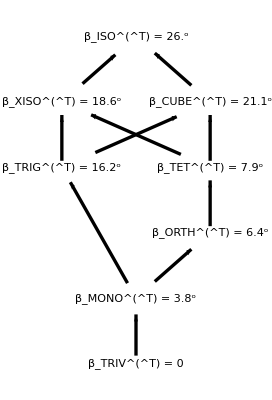

[T] = 1(50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

#### Table 2, column An00

```mathematica
CmatBrownAn00=CmatBrown;
TmatBrownAn00 = TmatOfCmat[CmatBrown];
MatrixNote[TmatBrownAn00]="T is BrownAn00"
MatrixShortNote[TmatBrownAn00]="An00"
PrintVoigt[TmatBrownAn00];
```

T is BrownAn00

An00

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.454 = 26.037^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

```mathematica
contours[TmatBrownAn00]=contours[TmatBrown]
MaxForScaling[TmatBrownAn00]=MaxForScaling[TmatBrown]
```

{0,2,4,6,8,10,12,14,16,18,20,22,24}

22

```mathematica
tpert[TmatBrownAn00]=tpert[TmatBrown]
```

0.66

#### BrownAn00 perturbed to its extreme

```mathematica
Tmat1=TmatBrownAn00;
Tmat2=Closest[TmatBrownAn00,ISO];
t1=-tpert[TmatBrownAn00];
TmatBrownAn00Pert=(1-t1) Tmat1+t1 Tmat2;
```

```mathematica
MatrixNote[TmatBrownAn00Pert]="T is BrownAn00Pert"
MatrixShortNote[TmatBrownAn00Pert]="An00p"
PrintVoigt[TmatBrownAn00Pert];
```

T is BrownAn00Pert

An00p

The [T]_𝔹𝔹 matrix is (28.308 | -7.968 | -23.904 | -15.438 | 18.1138 | -11.7918
-7.968 | 34.616 | 1.992 | -9.13 | -24.0559 | -3.524
-23.904 | 1.992 | 56.86 | -9.13 | 11.0216 | -22.6349
-15.438 | -9.13 | -9.13 | 101.514 | 79.9307 | 61.3989
18.1138 | -24.0559 | 11.0216 | 79.9307 | 193.035 | -30.6752
-11.7918 | -3.524 | -22.6349 | 61.3989 | -30.6752 | 189.267)

The eigenvalues are: {243.339,223.134,71.2524,38.8629,26.5166,0.494292}

The Voigt matrix is (35.278 | 30.044 | 27.056 | 8.134 | -3.818 | -1.494
30.044 | 227.838 | -15.108 | -7.304 | -12.948 | -10.624
27.056 | -15.108 | 220.7 | -15.272 | 12.45 | -15.604
8.134 | -7.304 | -15.272 | 14.154 | -3.984 | -11.952
-3.818 | -12.948 | 12.45 | -3.984 | 17.308 | 0.996
-1.494 | -10.624 | -15.604 | -11.952 | 0.996 | 28.43)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 214.796   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.681 = 39.04^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

```mathematica
cmin=0;cmax=36; dc=3;
contours[TmatBrownAn00Pert]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn00Pert]=cmax-dc;
```

```mathematica
tpert[TmatBrownAn00Pert]=0.;
```

#### Table 2, column An25

```mathematica
CmatBrownAn25=({{87.1, 43.9, 35.4, 6.1, -0.4, -0.6}, {43.9, 174.9, 18., -5.9, -2.9, -6.5}, {35.4, 18., 166.1, -2.9, 4.6, -10.7}, {6.1, -5.9, -2.9, 22.9, -1.3, -5.2}, {-0.4, -2.9, 4.6, -1.3, 29., 0.8}, {-0.6, -6.5, -10.7, -5.2, 0.8, 35.}});
TmatBrownAn25 = TmatOfCmat[CmatBrownAn25];
MatrixNote[TmatBrownAn25]="T is BrownAn25"
MatrixShortNote[TmatBrownAn25]="An25"
PrintVoigt[TmatBrownAn25];
```

T is BrownAn25

An25

The [T]_𝔹𝔹 matrix is (45.8 | -2.6 | -10.4 | -12. | 3.4641 | -2.20454
-2.6 | 58. | 1.6 | -2.5 | -7.21688 | 1.06145
-10.4 | 1.6 | 70. | -5.9 | 8.25611 | -14.5336
-12. | -2.5 | -5.9 | 87.1 | 35.3916 | 28.7407
3.4641 | -7.21688 | 8.25611 | 35.3916 | 133.433 | -8.43814
-2.20454 | 1.06145 | -14.5336 | 28.7407 | -8.43814 | 207.567)

The eigenvalues are: {215.82,153.063,72.9576,68.3963,56.5929,35.0705}

The Voigt matrix is (87.1 | 43.9 | 35.4 | 6.1 | -0.4 | -0.6
43.9 | 174.9 | 18. | -5.9 | -2.9 | -6.5
35.4 | 18. | 166.1 | -2.9 | 4.6 | -10.7
6.1 | -5.9 | -2.9 | 22.9 | -1.3 | -5.2
-0.4 | -2.9 | 4.6 | -1.3 | 29. | 0.8
-0.6 | -6.5 | -10.7 | -5.2 | 0.8 | 35.)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 101.274   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.356 = 20.4^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (78.8667 | 0. | 0. | 0. | 0. | 0.
0. | 78.8667 | 0. | 0. | 0. | 0.
0. | 0. | 78.8667 | 0. | 0. | 0.
0. | 0. | 0. | 78.8667 | 0. | 0.
0. | 0. | 0. | 0. | 78.8667 | 0.
0. | 0. | 0. | 0. | 0. | 207.567)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 42.9 and μ = 39.4333, Poisson is 0.260526

```mathematica
cmin=0;cmax=18; dc=2;
contours[TmatBrownAn25]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn25]=cmax-dc;
```

```mathematica
tpert[TmatBrownAn25]=0.66;
```

#### Table 2, column An37

```mathematica
CmatBrownAn37=({{96.2, 46.1, 38.4, 5.9, -0.2, -0.4}, {46.1, 189.4, 15.4, -7., -5.1, -6.8}, {38.4, 15.4, 171.9, 2.2, 7.2, -9.8}, {5.9, -7., 2.2, 23.6, -1.1, -4.8}, {-0.2, -5.1, 7.2, -1.1, 33.1, 1.4}, {-0.4, -6.8, -9.8, -4.8, 1.4, 35.5}});
TmatBrownAn37 = TmatOfCmat[CmatBrownAn37];
MatrixNote[TmatBrownAn37]="T is BrownAn37"
MatrixShortNote[TmatBrownAn37]="An37"
PrintVoigt[TmatBrownAn37];
```

T is BrownAn37

An37

The [T]_𝔹𝔹 matrix is (47.2 | -2.2 | -9.6 | -12.9 | -3.17543 | 0.898146
-2.2 | 66.2 | 2.8 | -4.9 | -11.3738 | 1.55134
-9.6 | 2.8 | 71. | -6.4 | 7.15914 | -13.8804
-12.9 | -4.9 | -6.4 | 96.7 | 40.1836 | 28.659
-3.17543 | -11.3738 | 7.15914 | 40.1836 | 141.7 | -4.6669
0.898146 | 1.55134 | -13.8804 | 28.659 | -4.6669 | 219.1)

The eigenvalues are: {227.095,166.063,75.7461,72.0686,62.1546,38.772}

The Voigt matrix is (96.2 | 46.1 | 38.4 | 5.9 | -0.2 | -0.4
46.1 | 189.4 | 15.4 | -7. | -5.1 | -6.8
38.4 | 15.4 | 171.9 | 2.2 | 7.2 | -9.8
5.9 | -7. | 2.2 | 23.6 | -1.1 | -4.8
-0.2 | -5.1 | 7.2 | -1.1 | 33.1 | 1.4
-0.4 | -6.8 | -9.8 | -4.8 | 1.4 | 35.5)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 108.122   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.358 = 20.49^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (84.56 | 0. | 0. | 0. | 0. | 0.
0. | 84.56 | 0. | 0. | 0. | 0.
0. | 0. | 84.56 | 0. | 0. | 0.
0. | 0. | 0. | 84.56 | 0. | 0.
0. | 0. | 0. | 0. | 84.56 | 0.
0. | 0. | 0. | 0. | 0. | 219.1)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 44.8467 and μ = 42.28, Poisson is 0.257365

```mathematica
cmin=0;cmax=18; dc=2;
contours[TmatBrownAn37]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn37]=cmax-dc;
```

```mathematica
tpert[TmatBrownAn37]=0.66;
```

#### Table 2, column An48

```mathematica
CmatBrownAn48=({{104.6, 51.5, 43.9, 6.5, 0.1, -0.8}, {51.5, 201.4, 14.5, -2.4, -4.8, -9.9}, {43.9, 14.5, 172.8, -0.4, 6.9, -5.7}, {6.5, -2.4, -0.4, 22.9, -1., -3.8}, {0.1, -4.8, 6.9, -1., 33., 2.1}, {-0.8, -9.9, -5.7, -3.8, 2.1, 35.6}});
TmatBrownAn48 = TmatOfCmat[CmatBrownAn48];
MatrixNote[TmatBrownAn48]="T is BrownAn48"
MatrixShortNote[TmatBrownAn48]="An48"
PrintVoigt[TmatBrownAn48];
```

T is BrownAn48

An48

The [T]_𝔹𝔹 matrix is (45.8 | -2. | -7.6 | -8.9 | 2.82902 | 3.02104
-2. | 66. | 4.2 | -4.9 | -10.681 | 1.79629
-7.6 | 4.2 | 71.2 | -9.1 | 0.404145 | -13.3905
-8.9 | -4.9 | -9.1 | 101.5 | 44.9179 | 27.5159
2.82902 | -10.681 | 0.404145 | 44.9179 | 144.433 | 1.17851
3.02104 | 1.79629 | -13.3905 | 27.5159 | 1.17851 | 232.867)

The eigenvalues are: {240.97,170.587,76.3638,72.1154,62.0117,39.7521}

The Voigt matrix is (104.6 | 51.5 | 43.9 | 6.5 | 0.1 | -0.8
51.5 | 201.4 | 14.5 | -2.4 | -4.8 | -9.9
43.9 | 14.5 | 172.8 | -0.4 | 6.9 | -5.7
6.5 | -2.4 | -0.4 | 22.9 | -1. | -3.8
0.1 | -4.8 | 6.9 | -1. | 33. | 2.1
-0.8 | -9.9 | -5.7 | -3.8 | 2.1 | 35.6)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 112.252   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.356 = 20.41^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (85.7867 | 0. | 0. | 0. | 0. | 0.
0. | 85.7867 | 0. | 0. | 0. | 0.
0. | 0. | 85.7867 | 0. | 0. | 0.
0. | 0. | 0. | 85.7867 | 0. | 0.
0. | 0. | 0. | 0. | 85.7867 | 0.
0. | 0. | 0. | 0. | 0. | 232.867)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 49.0267 and μ = 42.8933, Poisson is 0.266681

```mathematica
cmin=0;cmax=18; dc=2;
contours[TmatBrownAn48]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn48]=cmax-dc;
```

```mathematica
tpert[TmatBrownAn48]=0.66;
```

#### Table 2, column An60

```mathematica
CmatBrownAn60=({{109.3, 53.1, 42.1, 7.6, 1.2, -7.7}, {53.1, 185.5, 21.9, -2.9, 0.7, -6.8}, {42.1, 21.9, 164.1, 0.2, 2.5, 0.7}, {7.6, -2.9, 0.2, 22.2, 0.2, 1.4}, {1.2, 0.7, 2.5, 0.2, 33.1, 2.8}, {-7.7, -6.8, 0.7, 1.4, 2.8, 36.8}});
TmatBrownAn60 = TmatOfCmat[CmatBrownAn60];
MatrixNote[TmatBrownAn60]="T is BrownAn60"
MatrixShortNote[TmatBrownAn60]="An60"
PrintVoigt[TmatBrownAn60];
```

T is BrownAn60

An60

The [T]_𝔹𝔹 matrix is (44.4 | 0.4 | 2.8 | -10.5 | 2.48261 | 4.00083
0.4 | 66.2 | 5.6 | -0.5 | -1.78979 | 3.59258
2.8 | 5.6 | 73.6 | 0.9 | -9.17987 | -11.2677
-10.5 | -0.5 | 0.9 | 94.3 | 33.6595 | 22.8619
2.48261 | -1.78979 | -9.17987 | 33.6595 | 133.567 | 2.07418
4.00083 | 3.59258 | -11.2677 | 22.8619 | 2.07418 | 231.033)

The eigenvalues are: {236.248,151.495,80.9577,72.0631,62.4015,39.9345}

The Voigt matrix is (109.3 | 53.1 | 42.1 | 7.6 | 1.2 | -7.7
53.1 | 185.5 | 21.9 | -2.9 | 0.7 | -6.8
42.1 | 21.9 | 164.1 | 0.2 | 2.5 | 0.7
7.6 | -2.9 | 0.2 | 22.2 | 0.2 | 1.4
1.2 | 0.7 | 2.5 | 0.2 | 33.1 | 2.8
-7.7 | -6.8 | 0.7 | 1.4 | 2.8 | 36.8)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 93.0792   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.305 = 17.48^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.4133 | 0. | 0. | 0. | 0. | 0.
0. | 82.4133 | 0. | 0. | 0. | 0.
0. | 0. | 82.4133 | 0. | 0. | 0.
0. | 0. | 0. | 82.4133 | 0. | 0.
0. | 0. | 0. | 0. | 82.4133 | 0.
0. | 0. | 0. | 0. | 0. | 231.033)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 49.54 and μ = 41.2067, Poisson is 0.272958

```mathematica
cmin=0;cmax=16; dc=2;
contours[TmatBrownAn60]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn60]=cmax-dc;
```

```mathematica
tpert[TmatBrownAn60]=0.66;
```

#### Table 2, column An67

```mathematica
CmatBrownAn67=({{120.3, 54.4, 40.8, 9.2, 2.3, -10.1}, {54.4, 193.5, 16.1, 0.9, 3.1, -2.9}, {40.8, 16.1, 171.9, -0.9, 2.2, -0.3}, {9.2, 0.9, -0.9, 24., 0.7, 0.3}, {2.3, 3.1, 2.2, 0.7, 35.5, 3.2}, {-10.1, -2.9, -0.3, 0.3, 3.2, 37.3}});
TmatBrownAn67 = TmatOfCmat[CmatBrownAn67];
MatrixNote[TmatBrownAn67]="T is BrownAn67"
MatrixShortNote[TmatBrownAn67]="An67"
PrintVoigt[TmatBrownAn67];
```

T is BrownAn67

An67

The [T]_𝔹𝔹 matrix is (48. | 1.4 | 0.6 | -8.3 | 6.87047 | 7.51177
1.4 | 71. | 6.4 | 0.8 | 0.57735 | 6.20537
0.6 | 6.4 | 74.6 | 7.2 | -7.15914 | -10.8594
-8.3 | 0.8 | 7.2 | 102.5 | 35.3916 | 19.8
6.87047 | 0.57735 | -7.15914 | 35.3916 | 147.1 | 5.16188
7.51177 | 6.20537 | -10.8594 | 19.8 | 5.16188 | 236.1)

The eigenvalues are: {241.274,164.002,91.3898,75.5333,63.3167,43.7846}

The Voigt matrix is (120.3 | 54.4 | 40.8 | 9.2 | 2.3 | -10.1
54.4 | 193.5 | 16.1 | 0.9 | 3.1 | -2.9
40.8 | 16.1 | 171.9 | -0.9 | 2.2 | -0.3
9.2 | 0.9 | -0.9 | 24. | 0.7 | 0.3
2.3 | 3.1 | 2.2 | 0.7 | 35.5 | 3.2
-10.1 | -2.9 | -0.3 | 0.3 | 3.2 | 37.3)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 100.323   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.315 = 18.027^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (88.64 | 0. | 0. | 0. | 0. | 0.
0. | 88.64 | 0. | 0. | 0. | 0.
0. | 0. | 88.64 | 0. | 0. | 0.
0. | 0. | 0. | 88.64 | 0. | 0.
0. | 0. | 0. | 0. | 88.64 | 0.
0. | 0. | 0. | 0. | 0. | 236.1)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 49.1533 and μ = 44.32, Poisson is 0.262927

```mathematica
cmin=0;cmax=18; dc=2;
contours[TmatBrownAn67]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn67]=cmax-dc;
```

```mathematica
tpert[TmatBrownAn67]=0.66;
```

#### Table 2, column An78

```mathematica
CmatBrownAn78=({{120.4, 56.6, 49.9, 9., 3.2, -3.}, {56.6, 191.6, 26.3, 2.1, 5.4, -9.9}, {49.9, 26.3, 163.7, 1.7, 1.7, -8.1}, {9., 2.1, 1.7, 23.3, 0.8, 0.9}, {3.2, 5.4, 1.7, 0.8, 32.8, 4.5}, {-3., -9.9, -8.1, 0.9, 4.5, 35.}});
TmatBrownAn78 = TmatOfCmat[CmatBrownAn78];
MatrixNote[TmatBrownAn78]="T is BrownAn78"
MatrixShortNote[TmatBrownAn78]="An78"
PrintVoigt[TmatBrownAn78];
```

T is BrownAn78

An78

The [T]_𝔹𝔹 matrix is (46.6 | 1.6 | 1.8 | -6.9 | 4.4456 | 10.4512
1.6 | 65.6 | 9. | 2.2 | 3.00222 | 8.40991
1.8 | 9. | 70. | -6.9 | 1.90526 | -17.1464
-6.9 | 2.2 | -6.9 | 99.4 | 34.1791 | 19.4326
4.4456 | 3.00222 | 1.90526 | 34.1791 | 129.2 | 5.09117
10.4512 | 8.40991 | -17.1464 | 19.4326 | 5.09117 | 247.1)

The eigenvalues are: {252.902,149.465,82.9281,72.7627,56.297,43.5452}

The Voigt matrix is (120.4 | 56.6 | 49.9 | 9. | 3.2 | -3.
56.6 | 191.6 | 26.3 | 2.1 | 5.4 | -9.9
49.9 | 26.3 | 163.7 | 1.7 | 1.7 | -8.1
9. | 2.1 | 1.7 | 23.3 | 0.8 | 0.9
3.2 | 5.4 | 1.7 | 0.8 | 32.8 | 4.5
-3. | -9.9 | -8.1 | 0.9 | 4.5 | 35.)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 93.416   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.295 = 16.88^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.16 | 0. | 0. | 0. | 0. | 0.
0. | 82.16 | 0. | 0. | 0. | 0.
0. | 0. | 82.16 | 0. | 0. | 0.
0. | 0. | 0. | 82.16 | 0. | 0.
0. | 0. | 0. | 0. | 82.16 | 0.
0. | 0. | 0. | 0. | 0. | 247.1)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 54.98 and μ = 41.08, Poisson is 0.286175

```mathematica
cmin=0;cmax=16; dc=2;
contours[TmatBrownAn78]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn78]=cmax-dc;
```

```mathematica
tpert[TmatBrownAn78]=0.66;
```

#### Table 2, column An96

```mathematica
CmatBrownAn96=({{132.2, 64., 55.3, 9.5, 5.1, -10.8}, {64., 200.2, 31.9, 7.5, 3.5, -7.2}, {55.3, 31.9, 163.9, 6.6, 0.5, 1.6}, {9.5, 7.5, 6.6, 24.6, 3., -2.2}, {5.1, 3.5, 0.5, 3., 36.6, 5.2}, {-10.8, -7.2, 1.6, -2.2, 5.2, 36.}});
TmatBrownAn96 = TmatOfCmat[CmatBrownAn96];
MatrixNote[TmatBrownAn96]="T is BrownAn96"
MatrixShortNote[TmatBrownAn96]="An96"
PrintVoigt[TmatBrownAn96];
```

T is BrownAn96

An96

The [T]_𝔹𝔹 matrix is (49.2 | 6. | -4.4 | -2. | 2.19393 | 19.2693
6. | 73.2 | 10.4 | -1.6 | 4.38786 | 7.43012
-4.4 | 10.4 | 72. | 3.6 | -12.2398 | -13.3905
-2. | -1.6 | 3.6 | 102.2 | 33.1399 | 18.2079
2.19393 | 4.38786 | -12.2398 | 33.1399 | 127.867 | 10.7009
19.2693 | 7.43012 | -13.3905 | 18.2079 | 10.7009 | 266.233)

The eigenvalues are: {272.65,148.053,87.1567,80.6492,57.098,45.0931}

The Voigt matrix is (132.2 | 64. | 55.3 | 9.5 | 5.1 | -10.8
64. | 200.2 | 31.9 | 7.5 | 3.5 | -7.2
55.3 | 31.9 | 163.9 | 6.6 | 0.5 | 1.6
9.5 | 7.5 | 6.6 | 24.6 | 3. | -2.2
5.1 | 3.5 | 0.5 | 3. | 36.6 | 5.2
-10.8 | -7.2 | 1.6 | -2.2 | 5.2 | 36.)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 93.4734   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.278 = 15.95^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (84.8933 | 0. | 0. | 0. | 0. | 0.
0. | 84.8933 | 0. | 0. | 0. | 0.
0. | 0. | 84.8933 | 0. | 0. | 0.
0. | 0. | 0. | 84.8933 | 0. | 0.
0. | 0. | 0. | 0. | 84.8933 | 0.
0. | 0. | 0. | 0. | 0. | 266.233)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 60.4467 and μ = 42.4467, Poisson is 0.293735

```mathematica
cmin=0;cmax=16; dc=2;
contours[TmatBrownAn96]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn96]=cmax-dc;
```

```mathematica
tpert[TmatBrownAn96]=0.66;
```

## List of maps

#### Igel, Mora, Riollet (1995) [units of 10^11 dyne/cm^2 = 10^10 N/m^2; 1 dyne/cm^2 = 0.1 N/m^2] density is 1.0 g/cm^3 = 1000 kg/m^3

```mathematica
CmatIgel=({{10.0, 3.5, 2.5, -5.0, 0.1, 0.3}, {3.5, 8.0, 1.5, 0.2, -0.1, -0.15}, {2.5, 1.5, 6.0, 1.0, 0.4, 0.24}, {-5.0, 0.2, 1.0, 5.0, 0.35, 0.525}, {0.1, -0.1, 0.4, 0.35, 4.0, -1.0}, {0.3, -0.15, 0.24, 0.525, -1.0, 3.0}});
TmatIgel = TmatOfCmat[CmatIgel];
MatrixNote[TmatIgel]="T is Igel"
MatrixShortNote[TmatIgel]="Igel"
PrintVoigt[TmatIgel];
```

T is Igel

Igel

The [T]_𝔹𝔹 matrix is (10. | 0.7 | 1.05 | 5.2 | -3.92598 | -3.10269
0.7 | 8. | -2. | -0.2 | -0.46188 | 0.326599
1.05 | -2. | 6. | -0.45 | -0.190526 | 0.318434
5.2 | -0.2 | -0.45 | 5.5 | 0 | -1.22474
-3.92598 | -0.46188 | -0.190526 | 0 | 5.5 | 2.12132
-3.10269 | 0.326599 | 0.318434 | -1.22474 | 2.12132 | 13.)

The eigenvalues are: {17.7924,10.1797,9.22349,5.83219,4.30288,0.669364}

The Voigt matrix is (10. | 3.5 | 2.5 | -5. | 0.1 | 0.3
3.5 | 8. | 1.5 | 0.2 | -0.1 | -0.15
2.5 | 1.5 | 6. | 1. | 0.4 | 0.24
-5. | 0.2 | 1. | 5. | 0.35 | 0.525
0.1 | -0.1 | 0.4 | 0.35 | 4. | -1.
0.3 | -0.15 | 0.24 | 0.525 | -1. | 3.)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 12.0102   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.533 = 30.55^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (7. | 0. | 0. | 0. | 0. | 0.
0. | 7. | 0. | 0. | 0. | 0.
0. | 0. | 7. | 0. | 0. | 0.
0. | 0. | 0. | 7. | 0. | 0.
0. | 0. | 0. | 0. | 7. | 0.
0. | 0. | 0. | 0. | 0. | 13.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 2. and μ = 3.5, Poisson is 0.181818

```mathematica
cmin=0;cmax=30; dc=3;
contours[TmatIgel]=Range[cmin,cmax,dc];
MaxForScaling[TmatIgel]=cmax-dc;
```

```mathematica
tpert[TmatIgel]=0.10;
```

#### lattice for TmatIgel:

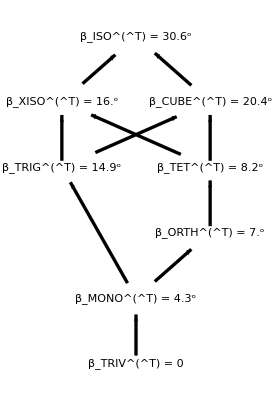

[T] = 1(10. | 0.7 | 1.05 | 5.2 | -3.92598 | -3.10269
0.7 | 8. | -2. | -0.2 | -0.46188 | 0.326599
1.05 | -2. | 6. | -0.45 | -0.190526 | 0.318434
5.2 | -0.2 | -0.45 | 5.5 | 0. | -1.22474
-3.92598 | -0.46188 | -0.190526 | 0. | 5.5 | 2.12132
-3.10269 | 0.326599 | 0.318434 | -1.22474 | 2.12132 | 13.)

#### Map used in SSA2023 by Aakash Gupta, generated from ES_FarFromMono.nb This map is far from MONO, and its Poisson parameter for its closest ISO is near 0.25.

```mathematica
TmatSSA2023=({{0.317082, -0.00658517, 0.227862, 0.219176, 0.114762, -0.244823}, {-0.00658517, 0.07346, -0.114858, -0.0207015, 0.0275774, -0.142342}, {0.227862, -0.114858, 0.420424, 0.212793, 0.0528639, 0.120438}, {0.219176, -0.0207015, 0.212793, 0.241031, 0.102265, -0.162818}, {0.114762, 0.0275774, 0.0528639, 0.102265, 0.0962717, -0.147361}, {-0.244823, -0.142342, 0.120438, -0.162818, -0.147361, 0.64901}});
```

```mathematica
MatrixNote[TmatSSA2023]="T is SSA2023"
MatrixShortNote[TmatSSA2023]="SSA"
PrintVoigt[TmatSSA2023];
```

T is SSA2023

SSA

The [T]_𝔹𝔹 matrix is (0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901)

The eigenvalues are: {0.965054,0.701544,0.060227,0.0422136,0.0158499,0.0123903}

The Voigt matrix is (0.357328 | 0.0423998 | 0.344492 | -0.176408 | -0.0397992 | -0.0419674
0.0423998 | 0.209533 | 0.0934665 | 0.0427684 | -0.0605007 | 0.170826
0.344492 | 0.0934665 | 0.419451 | -0.166206 | -0.0740327 | 0.0186476
-0.176408 | 0.0427684 | -0.166206 | 0.158541 | -0.00329258 | 0.113931
-0.0397992 | -0.0605007 | -0.0740327 | -0.00329258 | 0.03673 | -0.057429
-0.0419674 | 0.170826 | 0.0186476 | 0.113931 | -0.057429 | 0.210212)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 0.86278   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.806 = 46.19^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (0.229654 | 0. | 0. | 0. | 0. | 0.
0. | 0.229654 | 0. | 0. | 0. | 0.
0. | 0. | 0.229654 | 0. | 0. | 0.
0. | 0. | 0. | 0.229654 | 0. | 0.
0. | 0. | 0. | 0. | 0.229654 | 0.
0. | 0. | 0. | 0. | 0. | 0.64901)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 0.139785 and μ = 0.114827, Poisson is 0.274506

```mathematica
cmin=0;cmax=40; dc=4;
contours[TmatSSA2023]=Range[cmin,cmax,dc];
MaxForScaling[TmatSSA2023]=cmax-dc;
```

```mathematica
tpert[TmatSSA2023]=0.04;
```

#### lattice for TmatSSA2023:

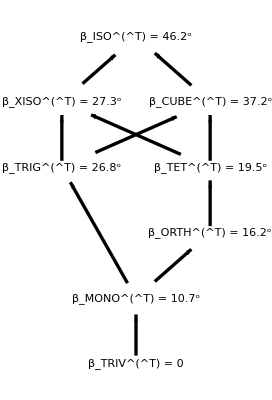

[T] = 1(0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901)

#### Russell, Gaherty, et al. (2019 JGR), Table 1 [units of GPa = 10^9 Pa = 10^9 N/m2]

```mathematica
CmatRussell=({{271.6149, 101.6837, 101.2700, 0, 0, −0.1902}, {101.6837, 233.9946, 99.9429, 0, 0, 0.3918}, {101.2700, 99.9429, 239.5542, 0, 0, 0.0071}, {0, 0, 0, 66.1769, 0.0452, 0}, {0, 0, 0, 0.0452, 74.6177, 0}, {−0.1902, 0.3918, 0.0071, 0, 0, 71.9655}});
TmatRussell = TmatOfCmat[CmatRussell];
MatrixNote[TmatRussell]="T is Russell"
MatrixShortNote[TmatRussell]="Russ"
PrintVoigt[TmatRussell];
```

T is Russell

Russ

The [T]_𝔹𝔹 matrix is (132.354 | 0.0904 | 0 | 0 | 0 | 0
0.0904 | 149.235 | 0 | 0 | 0 | 0
0 | 0 | 143.931 | 0.582 | 0.108195 | 0.170403
0 | 0 | 0.582 | 151.121 | -10.0938 | -15.9002
0 | 0 | 0.108195 | -10.0938 | 143.724 | 6.75419
0 | 0 | 0.170403 | -15.9002 | 6.75419 | 450.319)

The eigenvalues are: {451.334,157.213,149.236,143.943,136.605,132.353}

The Voigt matrix is (271.615 | 101.684 | 101.27 | 0 | 0 | -0.1902
101.684 | 233.995 | 99.9429 | 0 | 0 | 0.3918
101.27 | 99.9429 | 239.554 | 0 | 0 | 0.0071
0 | 0 | 0 | 66.1769 | 0.0452 | 0
0 | 0 | 0 | 0.0452 | 74.6177 | 0
-0.1902 | 0.3918 | 0.0071 | 0 | 0 | 71.9655)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 31.8626   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.057 = 3.29^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (144.073 | 0. | 0. | 0. | 0. | 0.
0. | 144.073 | 0. | 0. | 0. | 0.
0. | 0. | 144.073 | 0. | 0. | 0.
0. | 0. | 0. | 144.073 | 0. | 0.
0. | 0. | 0. | 0. | 144.073 | 0.
0. | 0. | 0. | 0. | 0. | 450.319)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 102.082 and μ = 72.0365, Poisson is 0.293139

```mathematica
cmin=0;cmax=3.25; dc=0.25;
contours[TmatRussell]=Range[cmin,cmax,dc];
MaxForScaling[TmatRussell]=cmax-dc;
```

```mathematica
tpert[TmatRussell]=11.29;
```

#### lattice for TmatRussell:

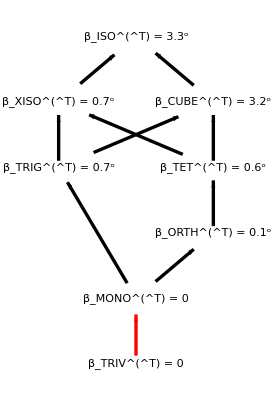

[T] = 1(132.354 | 0.0904 | 0. | 0. | 0. | 0.
0.0904 | 149.235 | 0. | 0. | 0. | 0.
0. | 0. | 143.931 | 0.582 | 0.108195 | 0.170403
0. | 0. | 0.582 | 151.121 | -10.0938 | -15.9002
0. | 0. | 0.108195 | -10.0938 | 143.724 | 6.75419
0. | 0. | 0.170403 | -15.9002 | 6.75419 | 450.319)

#### Lokajicek et al. (2021), Table 3, WG100, 0.1 MPa

```mathematica
CmatLokajicek=({{47.6, 16.7, 16.3, 0.1, -1.1, -2}, {16.7, 51.1, 16.8, 0, -0.6, -2.1}, {16.3, 16.8, 51.7, 0.2, -1.8, -1.2}, {0.1, 0, 0.2, 16.8, -0.2, -0.2}, {-1.1, -0.6, -1.8, -0.2, 16.8, 0.1}, {-2, -2.1, -1.2, -0.2, 0.1, 16.8}});
```

```mathematica
TmatLokajicek = TmatOfCmat[CmatLokajicek];
MatrixNote[TmatLokajicek]="T is Lokajicek"
MatrixShortNote[TmatLokajicek]="Loka"
PrintVoigt[TmatLokajicek];
```

T is Lokajicek

Loka

The [T]_𝔹𝔹 matrix is (33.6 | -0.4 | -0.4 | -0.1 | -0.173205 | 0.244949
-0.4 | 33.6 | 0.2 | 0.5 | 1.09697 | -2.85774
-0.4 | 0.2 | 33.6 | -0.1 | -0.981495 | -4.32743
-0.1 | 0.5 | -0.1 | 32.65 | 0.721688 | 1.63299
-0.173205 | 1.09697 | -0.981495 | 0.721688 | 34.4167 | -1.03709
0.244949 | -2.85774 | -4.32743 | 1.63299 | -1.03709 | 83.3333)

The eigenvalues are: {83.942,35.7219,34.0307,33.0105,32.4111,32.0838}

The Voigt matrix is (47.6 | 16.7 | 16.3 | 0.1 | -1.1 | -2.
16.7 | 51.1 | 16.8 | 0 | -0.6 | -2.1
16.3 | 16.8 | 51.7 | 0.2 | -1.8 | -1.2
0.1 | 0 | 0.2 | 16.8 | -0.2 | -0.2
-1.1 | -0.6 | -1.8 | -0.2 | 16.8 | 0.1
-2. | -2.1 | -1.2 | -0.2 | 0.1 | 16.8)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 8.34578   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.074 = 4.26^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (33.5733 | 0. | 0. | 0. | 0. | 0.
0. | 33.5733 | 0. | 0. | 0. | 0.
0. | 0. | 33.5733 | 0. | 0. | 0.
0. | 0. | 0. | 33.5733 | 0. | 0.
0. | 0. | 0. | 0. | 33.5733 | 0.
0. | 0. | 0. | 0. | 0. | 83.3333)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 16.5867 and μ = 16.7867, Poisson is 0.248502

```mathematica
cmin=0;cmax=4.5; dc=0.5;
contours[TmatLokajicek]=Range[cmin,cmax,dc];
MaxForScaling[TmatLokajicek]=cmax-dc;
```

```mathematica
tpert[TmatLokajicek]=0.00;  (* TBD *)
```

## Maps from Tape and Tape (2024)

#### TmatMar17 - exact expression

```mathematica
TmatPert=({{474, 22, 22, 18, 4, 10}, {22, 374, -22, 28, -16, -34}, {22, -22, 318, 6, -26, 6}, {18, 28, 6, 262, 8, 14}, {4, -16, -26, 8, 32, 42}, {10, -34, 6, 14, 42, 74}});
```

```mathematica
Urot=ZRot[-20.Degree].XRot[-30Degree];
TmatMar17exact=MatrixUbar[Urot].TmatPert.Transpose[MatrixUbar[Urot]];
PrintVoigt[TmatMar17exact];
```

The [T]_𝔹𝔹 matrix is (206.222 | -67.4376 | 17.062 | -15.8915 | 166.629 | -19.5016
-67.4376 | 352.858 | 32.2406 | 3.30383 | 61.6098 | -41.6251
17.062 | 32.2406 | 343.803 | 0.355839 | 73.5722 | -4.22981
-15.8915 | 3.30383 | 0.355839 | 269.972 | 88.7527 | 13.3226
166.629 | 61.6098 | 73.5722 | 88.7527 | 287.146 | 30.7189
-19.5016 | -41.6251 | -4.22981 | 13.3226 | 30.7189 | 74.)

The eigenvalues are: {483.05,387.082,311.329,256.996,91.5538,3.98966}

The Voigt matrix is (159.872 | -47.9805 | -32.4866 | 48.086 | -0.86007 | 19.3337
-47.9805 | 284.11 | -124.091 | 32.1945 | 2.44376 | 19.6896
-32.4866 | -124.091 | 187.135 | -104.165 | -52.5638 | -44.2037
48.086 | 32.1945 | -104.165 | 103.111 | -33.7188 | 8.53098
-0.86007 | 2.44376 | -52.5638 | -33.7188 | 176.429 | 16.1203
19.3337 | 19.6896 | -44.2037 | 8.53098 | 16.1203 | 171.902)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 350.348   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.49 = 28.06^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (292. | 0. | 0. | 0. | 0. | 0.
0. | 292. | 0. | 0. | 0. | 0.
0. | 0. | 292. | 0. | 0. | 0.
0. | 0. | 0. | 292. | 0. | 0.
0. | 0. | 0. | 0. | 292. | 0.
0. | 0. | 0. | 0. | 0. | 74.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = -72.6667 and μ = 146., Poisson is -0.495455

#### TmatMar17 (Eq. XX) - rounded to 0.01

```mathematica
TmatMar17=({{206.2, -67.4, 17.1, -15.9, 166.6, -19.5}, {-67.4, 352.9, 32.2, 3.3, 61.6, -41.6}, {17.1, 32.2, 343.8, 0.4, 73.6, -4.2}, {-15.9, 3.3, 0.4, 270.0, 88.8, 13.3}, {166.6, 61.6, 73.6, 88.8, 287.1, 30.7}, {-19.5, -41.6, -4.2, 13.3, 30.7, 74.0}});
```

```mathematica
MatrixNote[TmatMar17]="T is Mar17"
MatrixShortNote[TmatMar17]="Mar17"
PrintVoigt[TmatMar17];
```

T is Mar17

Mar17

The [T]_𝔹𝔹 matrix is (206.2 | -67.4 | 17.1 | -15.9 | 166.6 | -19.5
-67.4 | 352.9 | 32.2 | 3.3 | 61.6 | -41.6
17.1 | 32.2 | 343.8 | 0.4 | 73.6 | -4.2
-15.9 | 3.3 | 0.4 | 270. | 88.8 | 13.3
166.6 | 61.6 | 73.6 | 88.8 | 287.1 | 30.7
-19.5 | -41.6 | -4.2 | 13.3 | 30.7 | 74.)

The eigenvalues are: {483.066,387.05,311.312,257.018,91.543,4.01094}

The Voigt matrix is (159.861 | -48.0112 | -32.4304 | 48.0824 | -0.850741 | 19.3318
-48.0112 | 284.117 | -124.108 | 32.1824 | 2.44926 | 19.7318
-32.4304 | -124.108 | 187.122 | -104.147 | -52.5479 | -44.2076
48.0824 | 32.1824 | -104.147 | 103.1 | -33.7 | 8.55
-0.850741 | 2.44926 | -52.5479 | -33.7 | 176.45 | 16.1
19.3318 | 19.7318 | -44.2076 | 8.55 | 16.1 | 171.9)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 350.334   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.49 = 28.06^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (292. | 0. | 0. | 0. | 0. | 0.
0. | 292. | 0. | 0. | 0. | 0.
0. | 0. | 292. | 0. | 0. | 0.
0. | 0. | 0. | 292. | 0. | 0.
0. | 0. | 0. | 0. | 292. | 0.
0. | 0. | 0. | 0. | 0. | 74.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = -72.6667 and μ = 146., Poisson is -0.495455

```mathematica
cmin=0;cmax=27; dc=3;
contours[TmatMar17]=Range[cmin,cmax,dc];
MaxForScaling[TmatMar17]=cmax-dc;
```

```mathematica
tpert[TmatMar17]=0.01;
```

#### lattice for TmatMar17:

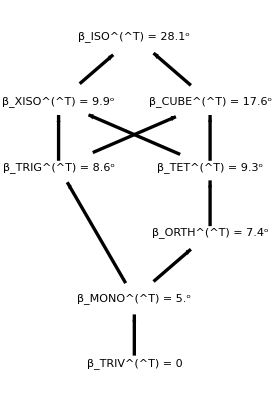

[T] = 1(206.222 | -67.4376 | 17.062 | -15.8915 | 166.629 | -19.5016
-67.4376 | 352.858 | 32.2406 | 3.30383 | 61.6098 | -41.6251
17.062 | 32.2406 | 343.803 | 0.355839 | 73.5722 | -4.22981
-15.8915 | 3.30383 | 0.355839 | 269.972 | 88.7527 | 13.3226
166.629 | 61.6098 | 73.5722 | 88.7527 | 287.146 | 30.7189
-19.5016 | -41.6251 | -4.22981 | 13.3226 | 30.7189 | 74.)

#### MONO map (Eq. XX)

```mathematica
TT24MONOa=({{1, 0, 0, 0, 0, 0}, {0, 2, 0, 0, 0, 0}, {0, 0, 3, 2, 1, 0}, {0, 0, 2, 4, 0, 0}, {0, 0, 1, 0, 5, 0}, {0, 0, 0, 0, 0, 6}});
```

```mathematica
MatrixNote[TT24MONOa]="T is TT24MONOa"
MatrixShortNote[TT24MONOa]="MONOa"
PrintVoigt[TT24MONOa];
```

T is TT24MONOa

MONOa

The [T]_𝔹𝔹 matrix is (1 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 3 | 2 | 1 | 0
0 | 0 | 2 | 4 | 0 | 0
0 | 0 | 1 | 0 | 5 | 0
0 | 0 | 0 | 0 | 0 | 6)

The eigenvalues are: {6,6,3+√3,2,3-√3,1}

The Voigt matrix is (29/6 | 5/6 | 1/3 | 0 | 0 | 1/6 (-6+√3)
5/6 | 29/6 | 1/3 | 0 | 0 | 1/6 (6+√3)
1/3 | 1/3 | 16/3 | 0 | 0 | -1/(√3)
0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
1/6 (-6+√3) | 1/6 (6+√3) | -1/(√3) | 0 | 0 | 3/2)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 2 √5   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.461 = 26.42^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (3. | 0. | 0. | 0. | 0. | 0.
0. | 3. | 0. | 0. | 0. | 0.
0. | 0. | 3. | 0. | 0. | 0.
0. | 0. | 0. | 3. | 0. | 0.
0. | 0. | 0. | 0. | 3. | 0.
0. | 0. | 0. | 0. | 0. | 6.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1 and μ = 3/2, Poisson is 1/5

#### MONO map (Eq. XX)

```mathematica
TT24MONOb=({{28, -2, 0, 0, 0, 0}, {-2, 61, 0, 0, 0, 0}, {0, 0, 71, -4, 6, 8}, {0, 0, -4, 68, 10, 0}, {0, 0, 6, 10, 62, -3}, {0, 0, 8, 0, -3, 59}});
```

```mathematica
MatrixNote[TT24MONOb]="T is TT24MONOb"
MatrixShortNote[TT24MONOb]="MONOb"
PrintVoigt[TT24MONOb];
```

T is TT24MONOb

MONOb

The [T]_𝔹𝔹 matrix is (28 | -2 | 0 | 0 | 0 | 0
-2 | 61 | 0 | 0 | 0 | 0
0 | 0 | 71 | -4 | 6 | 8
0 | 0 | -4 | 68 | 10 | 0
0 | 0 | 6 | 10 | 62 | -3
0 | 0 | 8 | 0 | -3 | 59)

The eigenvalues are: {Root76.5Root[16682408-1062803 #1+25080 #1^2-260 #1^3+#1^4&,4]76.52870371540331,Root75.5Root[16682408-1062803 #1+25080 #1^2-260 #1^3+#1^4&,3]75.48673732504164,1/2 (89+√1105),Root59.2Root[16682408-1062803 #1+25080 #1^2-260 #1^3+#1^4&,2]59.22570612086892,Root48.8Root[16682408-1062803 #1+25080 #1^2-260 #1^3+#1^4&,1]48.758852838686124,1/2 (89-√1105)}

The Voigt matrix is (64-√2-10/(√3) | -4-√2 | -1+1/(√2)+10/(√3) | 0 | 0 | 2+4 √(2/3)+√3
-4-√2 | 64-√2+10/(√3) | -1+1/(√2)-10/(√3) | 0 | 0 | -2+4 √(2/3)+√3
-1+1/(√2)+10/(√3) | -1+1/(√2)-10/(√3) | 61+2 √2 | 0 | 0 | (-6+4 √2)/(√3)
0 | 0 | 0 | 14 | -1 | 0
0 | 0 | 0 | -1 | 61/2 | 0
2+4 √(2/3)+√3 | -2+4 √(2/3)+√3 | (-6+4 √2)/(√3) | 0 | 0 | 71/2)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 2 √413   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.278 = 15.92^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (58. | 0. | 0. | 0. | 0. | 0.
0. | 58. | 0. | 0. | 0. | 0.
0. | 0. | 58. | 0. | 0. | 0.
0. | 0. | 0. | 58. | 0. | 0.
0. | 0. | 0. | 0. | 58. | 0.
0. | 0. | 0. | 0. | 0. | 59.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1/3 and μ = 29, Poisson is 1/176

#### ORTH map (Eq. XX)

```mathematica
TT24ORTHa=({{86, 0, 0, 0, 0, 0}, {0, 51, 0, 0, 0, 0}, {0, 0, 32, 0, 0, 0}, {0, 0, 0, 46, -20, 13}, {0, 0, 0, -20, 45, -2}, {0, 0, 0, 13, -2, 87}});
```

```mathematica
MatrixNote[TT24ORTHa]="T is TT24ORTHa"
MatrixShortNote[TT24ORTHa]="ORTHa"
PrintVoigt[TT24ORTHa];
```

T is TT24ORTHa

ORTHa

The [T]_𝔹𝔹 matrix is (86 | 0 | 0 | 0 | 0 | 0
0 | 51 | 0 | 0 | 0 | 0
0 | 0 | 32 | 0 | 0 | 0
0 | 0 | 0 | 46 | -20 | 13
0 | 0 | 0 | -20 | 45 | -2
0 | 0 | 0 | 13 | -2 | 87)

The eigenvalues are: {Root92.2Root[-138541+9414 #1-178 #1^2+#1^3&,3]92.17238684956311,86,Root61.3Root[-138541+9414 #1-178 #1^2+#1^3&,2]61.31301189642678,51,32,Root24.5Root[-138541+9414 #1-178 #1^2+#1^3&,1]24.514601254010113}

The Voigt matrix is (1/6 (357-4 √2+40 √3-26 √6) | 1/6 (81-4 √2) | 1/6 (84+2 √2-40 √3-13 √6) | 0 | 0 | 0
1/6 (81-4 √2) | 1/6 (357-4 √2-40 √3+26 √6) | 1/6 (84+2 √2+40 √3+13 √6) | 0 | 0 | 0
1/6 (84+2 √2-40 √3-13 √6) | 1/6 (84+2 √2+40 √3+13 √6) | 59+(4 √2)/3 | 0 | 0 | 0
0 | 0 | 0 | 43 | 0 | 0
0 | 0 | 0 | 0 | 51/2 | 0
0 | 0 | 0 | 0 | 0 | 16)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 2 √697   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.349 = 19.98^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (52. | 0. | 0. | 0. | 0. | 0.
0. | 52. | 0. | 0. | 0. | 0.
0. | 0. | 52. | 0. | 0. | 0.
0. | 0. | 0. | 52. | 0. | 0.
0. | 0. | 0. | 0. | 52. | 0.
0. | 0. | 0. | 0. | 0. | 87.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35/3 and μ = 26, Poisson is 35/226

#### ORTH map (Eq. XX)

```mathematica
TT24ORTHb=({{1, 0, 0, 0, 0, 0}, {0, 2, 0, 0, 0, 0}, {0, 0, 5, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}});
```

```mathematica
MatrixNote[TT24ORTHb]="T is TT24ORTHb"
MatrixShortNote[TT24ORTHb]="ORTHb"
PrintVoigt[TT24ORTHb];
```

T is TT24ORTHb

ORTHb

The [T]_𝔹𝔹 matrix is (1 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 5 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

The eigenvalues are: {5,2,1,1,1,1}

The Voigt matrix is (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 5/2)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 2 √3   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.647 = 37.09^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2. | 0. | 0. | 0. | 0. | 0.
0. | 2. | 0. | 0. | 0. | 0.
0. | 0. | 2. | 0. | 0. | 0.
0. | 0. | 0. | 2. | 0. | 0.
0. | 0. | 0. | 0. | 2. | 0.
0. | 0. | 0. | 0. | 0. | 1.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = -1/3 and μ = 1, Poisson is -1/4

#### TET map (Eq. XX)

```mathematica
TT24TETa=({{60, 0, 0, 0, 0, 0}, {0, 60, 0, 0, 0, 0}, {0, 0, 15, 0, 0, 0}, {0, 0, 0, 71, 0, 0}, {0, 0, 0, 0, 58, 6}, {0, 0, 0, 0, 6, 15}});
```

```mathematica
MatrixNote[TT24TETa]="T is TT24TETa"
MatrixShortNote[TT24TETa]="TETa"
PrintVoigt[TT24TETa];
```

T is TT24TETa

TETa

The [T]_𝔹𝔹 matrix is (60 | 0 | 0 | 0 | 0 | 0
0 | 60 | 0 | 0 | 0 | 0
0 | 0 | 15 | 0 | 0 | 0
0 | 0 | 0 | 71 | 0 | 0
0 | 0 | 0 | 0 | 58 | 6
0 | 0 | 0 | 0 | 6 | 15)

The eigenvalues are: {71,60,60,1/2 (73+√1993),15,1/2 (73-√1993)}

The Voigt matrix is (301/6+2 √2 | -125/6+2 √2 | -43/3-√2 | 0 | 0 | 0
-125/6+2 √2 | 301/6+2 √2 | -43/3-√2 | 0 | 0 | 0
-43/3-√2 | -43/3-√2 | 131/3-4 √2 | 0 | 0 | 0
0 | 0 | 0 | 30 | 0 | 0
0 | 0 | 0 | 0 | 30 | 0
0 | 0 | 0 | 0 | 0 | 15/2)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = √(9814/5)   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.356 = 20.42^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (52.8 | 0. | 0. | 0. | 0. | 0.
0. | 52.8 | 0. | 0. | 0. | 0.
0. | 0. | 52.8 | 0. | 0. | 0.
0. | 0. | 0. | 52.8 | 0. | 0.
0. | 0. | 0. | 0. | 52.8 | 0.
0. | 0. | 0. | 0. | 0. | 15.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = -63/5 and μ = 132/5, Poisson is -21/46

#### TET map (Eq. XX)

```mathematica
TT24TETb=({{2, 0, 0, 0, 0, 0}, {0, 2, 0, 0, 0, 0}, {0, 0, 3, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 2, 0}, {0, 0, 0, 0, 0, 1}});
```

```mathematica
MatrixNote[TT24TETb]="T is TT24TETb"
MatrixShortNote[TT24TETb]="TETb"
PrintVoigt[TT24TETb];
```

T is TT24TETb

TETb

The [T]_𝔹𝔹 matrix is (2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 1)

The eigenvalues are: {3,2,2,2,1,1}

The Voigt matrix is (7/6 | 1/6 | -1/3 | 0 | 0 | 0
1/6 | 7/6 | -1/3 | 0 | 0 | 0
-1/3 | -1/3 | 5/3 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 3/2)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = √2   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.299 = 17.15^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2. | 0. | 0. | 0. | 0. | 0.
0. | 2. | 0. | 0. | 0. | 0.
0. | 0. | 2. | 0. | 0. | 0.
0. | 0. | 0. | 2. | 0. | 0.
0. | 0. | 0. | 0. | 2. | 0.
0. | 0. | 0. | 0. | 0. | 1.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = -1/3 and μ = 1, Poisson is -1/4

## Maps from Tape and Tape (2022) – see ES_RefMatricesForCollage.nb

## Maps from Tape and Tape (2021)

#### TRIV (Eq. 23)

```mathematica
denominator=5;
TT21TRIV=1/denominator({{5, 0, 0, -2, 0, 0}, {0, 6, 0, 0, -2, 0}, {0, 0, 5, 0, 0, 0}, {-2, 0, 0, 5, 0, 0}, {0, -2, 0, 0, 6, 0}, {0, 0, 0, 0, 0, 6}});
```

```mathematica
MatrixNote[TT21TRIV]="T is TT21TRIV"
MatrixShortNote[TT21TRIV]="TRIV"
PrintVoigt[TT21TRIV];
```

T is TT21TRIV

TRIV

The [T]_𝔹𝔹 matrix is (1 | 0 | 0 | -2/5 | 0 | 0
0 | 6/5 | 0 | 0 | -2/5 | 0
0 | 0 | 1 | 0 | 0 | 0
-2/5 | 0 | 0 | 1 | 0 | 0
0 | -2/5 | 0 | 0 | 6/5 | 0
0 | 0 | 0 | 0 | 0 | 6/5)

The eigenvalues are: {8/5,7/5,6/5,1,4/5,3/5}

The Voigt matrix is (11/10 | 1/10 | 0 | 1/5 | -1/(5 √3) | 0
1/10 | 11/10 | 0 | -1/5 | -1/(5 √3) | 0
0 | 0 | 6/5 | 0 | 2/(5 √3) | 0
1/5 | -1/5 | 0 | 1/2 | 0 | 0
-1/(5 √3) | -1/(5 √3) | 2/(5 √3) | 0 | 3/5 | 0
0 | 0 | 0 | 0 | 0 | 1/2)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = (√(86/5))/5   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.298 = 17.1^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (1.08 | 0. | 0. | 0. | 0. | 0.
0. | 1.08 | 0. | 0. | 0. | 0.
0. | 0. | 1.08 | 0. | 0. | 0.
0. | 0. | 0. | 1.08 | 0. | 0.
0. | 0. | 0. | 0. | 1.08 | 0.
0. | 0. | 0. | 0. | 0. | 1.2)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1/25 and μ = 27/50, Poisson is 1/29

#### lattice for TT21TRIV:

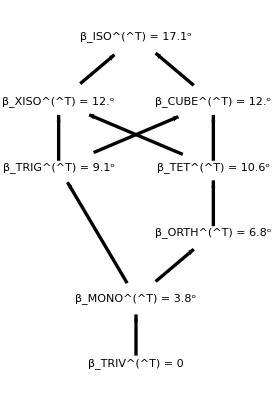

[T] = 1/5(5 | 0 | 0 | -2 | 0 | 0
0 | 6 | 0 | 0 | -2 | 0
0 | 0 | 5 | 0 | 0 | 0
-2 | 0 | 0 | 5 | 0 | 0
0 | -2 | 0 | 0 | 6 | 0
0 | 0 | 0 | 0 | 0 | 6)

#### MONO (Section 15.1)

```mathematica
denominator=80;
TT21MONO=1/denominator({{222, -12 √6, -82, 21 √6, -39 √2, 0}, {-12 √6, 196, 12 √6, 30, 10 √3, -16}, {-82, 12 √6, 222, 9 √6, -51 √2, 0}, {21 √6, 30, 9 √6, 242, -6 √3, -24}, {-39 √2, 10 √3, -51 √2, -6 √3, 254, -8 √3}, {0, -16, 0, -24, -8 √3, 304}});
```

```mathematica
MatrixNote[TT21MONO]="T is TT21MONO"
PrintVoigt[TT21MONO];
MatrixForm[N[TT21MONO]]
```

T is TT21MONO

The [T]_𝔹𝔹 matrix is (111/40 | -(3 √(3/2))/10 | -41/40 | (21 √(3/2))/40 | -39/(40 √2) | 0
-(3 √(3/2))/10 | 49/20 | (3 √(3/2))/10 | 3/8 | (√3)/8 | -1/5
-41/40 | (3 √(3/2))/10 | 111/40 | (9 √(3/2))/40 | -51/(40 √2) | 0
(21 √(3/2))/40 | 3/8 | (9 √(3/2))/40 | 121/40 | -(3 √3)/40 | -3/10
-39/(40 √2) | (√3)/8 | -51/(40 √2) | -(3 √3)/40 | 127/40 | -(√3)/10
0 | -1/5 | 0 | -3/10 | -(√3)/10 | 19/5)

The eigenvalues are: {4,4,4,3,2,1}

The Voigt matrix is (1/60 (203+4 √6) | 1/60 (17-2 √6) | 1/15 (2+√6) | -(17 √(3/2))/40 | -1/8-1/(5 √6) | -(13 √(3/2))/40
1/60 (17-2 √6) | 1/30 (97-4 √6) | 1/60 (17-2 √6) | (√(3/2))/10 | 1/4-1/(5 √6) | -(√(3/2))/10
1/15 (2+√6) | 1/60 (17-2 √6) | 1/60 (203+4 √6) | (13 √(3/2))/40 | -1/8-1/(5 √6) | (17 √(3/2))/40
-(17 √(3/2))/40 | (√(3/2))/10 | (13 √(3/2))/40 | 111/80 | -(3 √(3/2))/20 | -41/80
-1/8-1/(5 √6) | 1/4-1/(5 √6) | -1/8-1/(5 √6) | -(3 √(3/2))/20 | 49/40 | (3 √(3/2))/20
-(13 √(3/2))/40 | -(√(3/2))/10 | (17 √(3/2))/40 | -41/80 | (3 √(3/2))/20 | 111/80)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = (2 √(226/5))/5   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.349 = 19.97^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2.84 | 0. | 0. | 0. | 0. | 0.
0. | 2.84 | 0. | 0. | 0. | 0.
0. | 0. | 2.84 | 0. | 0. | 0.
0. | 0. | 0. | 2.84 | 0. | 0.
0. | 0. | 0. | 0. | 2.84 | 0.
0. | 0. | 0. | 0. | 0. | 3.8)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 8/25 and μ = 71/50, Poisson is 8/87

(2.775 | -0.367423 | -1.025 | 0.642991 | -0.689429 | 0.
-0.367423 | 2.45 | 0.367423 | 0.375 | 0.216506 | -0.2
-1.025 | 0.367423 | 2.775 | 0.275568 | -0.901561 | 0.
0.642991 | 0.375 | 0.275568 | 3.025 | -0.129904 | -0.3
-0.689429 | 0.216506 | -0.901561 | -0.129904 | 3.175 | -0.173205
0. | -0.2 | 0. | -0.3 | -0.173205 | 3.8)

#### lattice for TT21MONO:

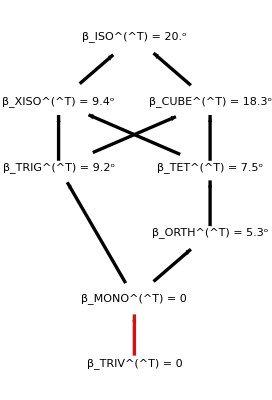

[T] = 1/80(222 | -12 √6 | -82 | 21 √6 | -39 √2 | 0
-12 √6 | 196 | 12 √6 | 30 | 10 √3 | -16
-82 | 12 √6 | 222 | 9 √6 | -51 √2 | 0
21 √6 | 30 | 9 √6 | 242 | -6 √3 | -24
-39 √2 | 10 √3 | -51 √2 | -6 √3 | 254 | -8 √3
0 | -16 | 0 | -24 | -8 √3 | 304)

#### ORTH (Section 15.2)

```mathematica
denominator=10;
TT21ORTH=1/denominator({{38, 18, 3 √2, -5 √2, -√6, -√8}, {18, 38, 3 √2, 5 √2, -√6, -√8}, {3 √2, 3 √2, 41, 0, -7 √3, 6}, {-5 √2, 5 √2, 0, 20, 0, 0}, {-√6, -√6, -7 √3, 0, 27, -2 √3}, {-√8, -√8, 6, 0, -2 √3, 56}});
```

```mathematica
MatrixNote[TT21ORTH]="T is TT21ORTH"
PrintVoigt[TT21ORTH];
MatrixForm[N[TT21ORTH]]
```

T is TT21ORTH

The [T]_𝔹𝔹 matrix is (19/5 | 9/5 | 3/(5 √2) | -1/(√2) | -(√(3/2))/5 | -(√2)/5
9/5 | 19/5 | 3/(5 √2) | 1/(√2) | -(√(3/2))/5 | -(√2)/5
3/(5 √2) | 3/(5 √2) | 41/10 | 0 | -(7 √3)/10 | 3/5
-1/(√2) | 1/(√2) | 0 | 2 | 0 | 0
-(√(3/2))/5 | -(√(3/2))/5 | -(7 √3)/10 | 0 | 27/10 | -(√3)/5
-(√2)/5 | -(√2)/5 | 3/5 | 0 | -(√3)/5 | 28/5)

The eigenvalues are: {6,6,4,3,2,1}

The Voigt matrix is (1/60 (199-4 √6) | 1/60 (79-4 √6) | 1/30 (29+√6) | -(-6+√6)/(15 √2) | -(9+√6)/(15 √2) | 1/20 (-7+2 √6)
1/60 (79-4 √6) | 1/60 (199-4 √6) | 1/30 (29+√6) | -(9+√6)/(15 √2) | -(-6+√6)/(15 √2) | 1/20 (-7+2 √6)
1/30 (29+√6) | 1/30 (29+√6) | 1/15 (55+2 √6) | -(-3+√6)/(15 √2) | -(-3+√6)/(15 √2) | 1/10 (7+√6)
-(-6+√6)/(15 √2) | -(9+√6)/(15 √2) | -(-3+√6)/(15 √2) | 19/10 | 9/10 | 3/(10 √2)
-(9+√6)/(15 √2) | -(-6+√6)/(15 √2) | -(-3+√6)/(15 √2) | 9/10 | 19/10 | 3/(10 √2)
1/20 (-7+2 √6) | 1/20 (-7+2 √6) | 1/10 (7+√6) | 3/(10 √2) | 3/(10 √2) | 41/20)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = (9 √(26/5))/5   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.419 = 23.98^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (3.28 | 0. | 0. | 0. | 0. | 0.
0. | 3.28 | 0. | 0. | 0. | 0.
0. | 0. | 3.28 | 0. | 0. | 0.
0. | 0. | 0. | 3.28 | 0. | 0.
0. | 0. | 0. | 0. | 3.28 | 0.
0. | 0. | 0. | 0. | 0. | 5.6)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 58/75 and μ = 41/25, Poisson is 29/181

(3.8 | 1.8 | 0.424264 | -0.707107 | -0.244949 | -0.282843
1.8 | 3.8 | 0.424264 | 0.707107 | -0.244949 | -0.282843
0.424264 | 0.424264 | 4.1 | 0. | -1.21244 | 0.6
-0.707107 | 0.707107 | 0. | 2. | 0. | 0.
-0.244949 | -0.244949 | -1.21244 | 0. | 2.7 | -0.34641
-0.282843 | -0.282843 | 0.6 | 0. | -0.34641 | 5.6)

#### lattice for TT21ORTH:

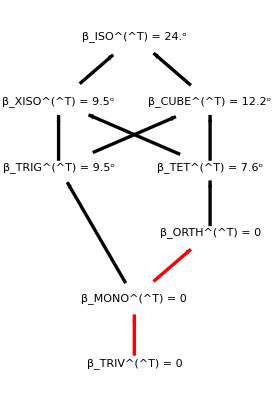

[T] = 1/10(38 | 18 | 3 √2 | -5 √2 | -√6 | -2 √2
18 | 38 | 3 √2 | 5 √2 | -√6 | -2 √2
3 √2 | 3 √2 | 41 | 0 | -7 √3 | 6
-5 √2 | 5 √2 | 0 | 20 | 0 | 0
-√6 | -√6 | -7 √3 | 0 | 27 | -2 √3
-2 √2 | -2 √2 | 6 | 0 | -2 √3 | 56)

#### TET (Section 15.3)

```mathematica
denominator=64;
TT21TET=1/denominator({{168, 4 √6, -40, 6 √6, 6 √2, 0}, {4 √6, 324, -4 √6, -42, -14 √3, 16 √3}, {-40, -4 √6, 168, -6 √6, -6 √2, 0}, {6 √6, -42, -6 √6, 233, 35 √3, -8 √3}, {6 √2, -14 √3, -6 √2, 35 √3, 163, -8}, {0, 16 √3, 0, -8 √3, -8, 352}});
```

```mathematica
MatrixNote[TT21TET]="T is TT21TET"
PrintVoigt[TT21TET];
MatrixForm[N[TT21TET]]
```

T is TT21TET

The [T]_𝔹𝔹 matrix is (21/8 | (√(3/2))/8 | -5/8 | (3 √(3/2))/16 | 3/(16 √2) | 0
(√(3/2))/8 | 81/16 | -(√(3/2))/8 | -21/32 | -(7 √3)/32 | (√3)/4
-5/8 | -(√(3/2))/8 | 21/8 | -(3 √(3/2))/16 | -3/(16 √2) | 0
(3 √(3/2))/16 | -21/32 | -(3 √(3/2))/16 | 233/64 | (35 √3)/64 | -(√3)/8
3/(16 √2) | -(7 √3)/32 | -3/(16 √2) | (35 √3)/64 | 163/64 | -1/8
0 | (√3)/4 | 0 | -(√3)/8 | -1/8 | 11/2)

The eigenvalues are: {6,5,4,3,2,2}

The Voigt matrix is (1/96 (339+8 √2) | 1/48 (21-2 √2) | 1/96 (147+8 √2) | -(√(3/2))/16 | 1/32 (7+4 √2) | (√(3/2))/16
1/48 (21-2 √2) | 37/8-1/(3 √2) | 1/48 (21-2 √2) | (√(3/2))/8 | 1/16 (-7+2 √2) | -(√(3/2))/8
1/96 (147+8 √2) | 1/48 (21-2 √2) | 1/96 (339+8 √2) | -(√(3/2))/16 | 1/32 (7+4 √2) | (√(3/2))/16
-(√(3/2))/16 | (√(3/2))/8 | -(√(3/2))/16 | 21/16 | (√(3/2))/16 | -5/16
1/32 (7+4 √2) | 1/16 (-7+2 √2) | 1/32 (7+4 √2) | (√(3/2))/16 | 81/32 | -(√(3/2))/16
(√(3/2))/16 | -(√(3/2))/8 | (√(3/2))/16 | -5/16 | -(√(3/2))/16 | 21/16)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = √(93/10)   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.32 = 18.33^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (3.3 | 0. | 0. | 0. | 0. | 0.
0. | 3.3 | 0. | 0. | 0. | 0.
0. | 0. | 3.3 | 0. | 0. | 0.
0. | 0. | 0. | 3.3 | 0. | 0.
0. | 0. | 0. | 0. | 3.3 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 11/15 and μ = 33/20, Poisson is 2/13

(2.625 | 0.153093 | -0.625 | 0.22964 | 0.132583 | 0.
0.153093 | 5.0625 | -0.153093 | -0.65625 | -0.378886 | 0.433013
-0.625 | -0.153093 | 2.625 | -0.22964 | -0.132583 | 0.
0.22964 | -0.65625 | -0.22964 | 3.64063 | 0.947215 | -0.216506
0.132583 | -0.378886 | -0.132583 | 0.947215 | 2.54688 | -0.125
0. | 0.433013 | 0. | -0.216506 | -0.125 | 5.5)

#### lattice for TT21TET:

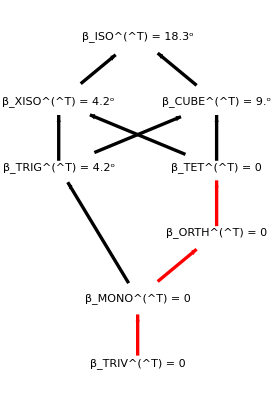

[T] = 1/64(168 | 4 √6 | -40 | 6 √6 | 6 √2 | 0
4 √6 | 324 | -4 √6 | -42 | -14 √3 | 16 √3
-40 | -4 √6 | 168 | -6 √6 | -6 √2 | 0
6 √6 | -42 | -6 √6 | 233 | 35 √3 | -8 √3
6 √2 | -14 √3 | -6 √2 | 35 √3 | 163 | -8
0 | 16 √3 | 0 | -8 √3 | -8 | 352)

#### XISO (Section 15.4)

```mathematica
denominator=128;
TT21XISO=1/denominator({{532, 92 √3, 122, -2 √3, -60, 48}, {92 √3, 348, -2 √3, 126, -20 √3, 16 √3}, {122, -2 √3, 349, 31 √3, -126, 24}, {-2 √3, 126, 31 √3, 287, -42 √3, 8 √3}, {-60, -20 √3, -126, -42 √3, 212, -16}, {48, 16 √3, 24, 8 √3, -16, 704}});
```

```mathematica
MatrixNote[TT21XISO]="T is TT21XISO"
PrintVoigt[TT21XISO];
MatrixForm[N[TT21XISO]]
```

T is TT21XISO

The [T]_𝔹𝔹 matrix is (133/32 | (23 √3)/32 | 61/64 | -(√3)/64 | -15/32 | 3/8
(23 √3)/32 | 87/32 | -(√3)/64 | 63/64 | -(5 √3)/32 | (√3)/8
61/64 | -(√3)/64 | 349/128 | (31 √3)/128 | -63/64 | 3/16
-(√3)/64 | 63/64 | (31 √3)/128 | 287/128 | -(21 √3)/64 | (√3)/16
-15/32 | -(5 √3)/32 | -63/64 | -(21 √3)/64 | 53/32 | -1/8
3/8 | (√3)/8 | 3/16 | (√3)/16 | -1/8 | 11/2)

The eigenvalues are: {6,5,3,3,1,1}

The Voigt matrix is (1/768 (2733-80 √2) | 1/768 (759-32 √2) | 1/192 (183-2 √2) | 1/128 √3 (-9+8 √2) | 1/128 (-73+8 √2) | 1/256 √3 (-73+8 √2)
1/768 (759-32 √2) | 1/768 (2229+16 √2) | 1/192 (309+10 √2) | 1/128 √3 (-11+8 √2) | 1/128 (53+8 √2) | 1/256 √3 (-11+8 √2)
1/192 (183-2 √2) | 1/192 (309+10 √2) | 1/48 (141+4 √2) | 1/32 √(3/2) (4+5 √2) | 1/32 (5+2 √2) | 1/64 √(3/2) (4+21 √2)
1/128 √3 (-9+8 √2) | 1/128 √3 (-11+8 √2) | 1/32 √(3/2) (4+5 √2) | 133/64 | (23 √3)/64 | 61/128
1/128 (-73+8 √2) | 1/128 (53+8 √2) | 1/32 (5+2 √2) | (23 √3)/64 | 87/64 | -(√3)/128
1/256 √3 (-73+8 √2) | 1/256 √3 (-11+8 √2) | 1/64 √(3/2) (4+21 √2) | 61/128 | -(√3)/128 | 349/256)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = √(143/10)   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.434 = 24.85^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2.7 | 0. | 0. | 0. | 0. | 0.
0. | 2.7 | 0. | 0. | 0. | 0.
0. | 0. | 2.7 | 0. | 0. | 0.
0. | 0. | 0. | 2.7 | 0. | 0.
0. | 0. | 0. | 0. | 2.7 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 14/15 and μ = 27/20, Poisson is 28/137

(4.15625 | 1.24491 | 0.953125 | -0.0270633 | -0.46875 | 0.375
1.24491 | 2.71875 | -0.0270633 | 0.984375 | -0.270633 | 0.216506
0.953125 | -0.0270633 | 2.72656 | 0.419481 | -0.984375 | 0.1875
-0.0270633 | 0.984375 | 0.419481 | 2.24219 | -0.568329 | 0.108253
-0.46875 | -0.270633 | -0.984375 | -0.568329 | 1.65625 | -0.125
0.375 | 0.216506 | 0.1875 | 0.108253 | -0.125 | 5.5)

#### lattice for TT21XISO:

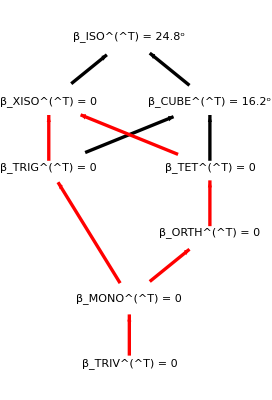

[T] = 1/128(532 | 92 √3 | 122 | -2 √3 | -60 | 48
92 √3 | 348 | -2 √3 | 126 | -20 √3 | 16 √3
122 | -2 √3 | 349 | 31 √3 | -126 | 24
-2 √3 | 126 | 31 √3 | 287 | -42 √3 | 8 √3
-60 | -20 √3 | -126 | -42 √3 | 212 | -16
48 | 16 √3 | 24 | 8 √3 | -16 | 704)

#### CUBE (Section 15.5)

```mathematica
denominator=36;
TT21CUBE=1/denominator({{52, 4, 16, -6, -2 √3, 0}, {4, 64, 4, 12, 4 √3, 0}, {16, 4, 52, -6, -2 √3, 0}, {-6, 12, -6, 45, 3 √3, 0}, {-2 √3, 4 √3, -2 √3, 3 √3, 39, 0}, {0, 0, 0, 0, 0, 108}});
```

```mathematica
MatrixNote[TT21CUBE]="T is TT21CUBE"
PrintVoigt[TT21CUBE];
MatrixForm[N[TT21CUBE]]
```

T is TT21CUBE

The [T]_𝔹𝔹 matrix is (13/9 | 1/9 | 4/9 | -1/6 | -1/(6 √3) | 0
1/9 | 16/9 | 1/9 | 1/3 | 1/(3 √3) | 0
4/9 | 1/9 | 13/9 | -1/6 | -1/(6 √3) | 0
-1/6 | 1/3 | -1/6 | 5/4 | 1/(4 √3) | 0
-1/(6 √3) | 1/(3 √3) | -1/(6 √3) | 1/(4 √3) | 13/12 | 0
0 | 0 | 0 | 0 | 0 | 3)

The eigenvalues are: {3,2,2,1,1,1}

The Voigt matrix is (31/18 | 5/9 | 13/18 | 1/18 | -1/9 | 1/18
5/9 | 17/9 | 5/9 | -1/9 | 2/9 | -1/9
13/18 | 5/9 | 31/18 | 1/18 | -1/9 | 1/18
1/18 | -1/9 | 1/18 | 13/18 | 1/18 | 2/9
-1/9 | 2/9 | -1/9 | 1/18 | 8/9 | 1/18
1/18 | -1/9 | 1/18 | 2/9 | 1/18 | 13/18)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = √(6/5)   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.247 = 14.18^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (1.4 | 0. | 0. | 0. | 0. | 0.
0. | 1.4 | 0. | 0. | 0. | 0.
0. | 0. | 1.4 | 0. | 0. | 0.
0. | 0. | 0. | 1.4 | 0. | 0.
0. | 0. | 0. | 0. | 1.4 | 0.
0. | 0. | 0. | 0. | 0. | 3.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 8/15 and μ = 7/10, Poisson is 8/37

(1.44444 | 0.111111 | 0.444444 | -0.166667 | -0.096225 | 0.
0.111111 | 1.77778 | 0.111111 | 0.333333 | 0.19245 | 0.
0.444444 | 0.111111 | 1.44444 | -0.166667 | -0.096225 | 0.
-0.166667 | 0.333333 | -0.166667 | 1.25 | 0.144338 | 0.
-0.096225 | 0.19245 | -0.096225 | 0.144338 | 1.08333 | 0.
0. | 0. | 0. | 0. | 0. | 3.)

#### lattice for TT21CUBE:

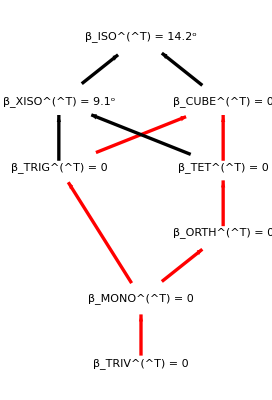

[T] = 1/36(52 | 4 | 16 | -6 | -2 √3 | 0
4 | 64 | 4 | 12 | 4 √3 | 0
16 | 4 | 52 | -6 | -2 √3 | 0
-6 | 12 | -6 | 45 | 3 √3 | 0
-2 √3 | 4 √3 | -2 √3 | 3 √3 | 39 | 0
0 | 0 | 0 | 0 | 0 | 108)

#### TRIG (Section 15.6)

```mathematica
denominator=16;
TT21TRIG=1/denominator({{4(8-√3), -8, 3 √2, -6 √2, -3 √6, 0}, {-8, 4(8+√3), 3 √2, 6 √2, -3 √6, 0}, {3 √2, 3 √2, 76, -2 √3, 12 √3, 4 √3}, {-6 √2, 6 √2, -2 √3, 24, 6, 0}, {-3 √6, -3 √6, 12 √3, 6, 52, 4}, {0, 0, 4 √3, 0, 4, 88}});
```

```mathematica
MatrixNote[TT21TRIG]="T is TT21TRIG"
PrintVoigt[TT21TRIG];
MatrixForm[N[TT21TRIG]]
```

T is TT21TRIG

The [T]_𝔹𝔹 matrix is (1/4 (8-√3) | -1/2 | 3/(8 √2) | -3/(4 √2) | -(3 √(3/2))/8 | 0
-1/2 | 1/4 (8+√3) | 3/(8 √2) | 3/(4 √2) | -(3 √(3/2))/8 | 0
3/(8 √2) | 3/(8 √2) | 19/4 | -(√3)/8 | (3 √3)/4 | (√3)/4
-3/(4 √2) | 3/(4 √2) | -(√3)/8 | 3/2 | 3/8 | 0
-(3 √(3/2))/8 | -(3 √(3/2))/8 | (3 √3)/4 | 3/8 | 13/4 | 1/4
0 | 0 | (√3)/4 | 0 | 1/4 | 11/2)

The eigenvalues are: {6,5,3,3,1,1}

The Voigt matrix is (1/24 (75+2 √2-3 √3) | 1/24 (39+2 √2) | 1/24 (18-√2+3 √3) | 3/(16 √2) | -9/(16 √2) | 1/16 (6+2 √2+√3)
1/24 (39+2 √2) | 1/24 (75+2 √2+3 √3) | 1/24 (18-√2-3 √3) | -9/(16 √2) | 3/(16 √2) | 1/16 (6+2 √2-√3)
1/24 (18-√2+3 √3) | 1/24 (18-√2-3 √3) | 4-1/(3 √2) | 3/(8 √2) | 3/(8 √2) | 1/8 (-6+√2)
3/(16 √2) | -9/(16 √2) | 3/(8 √2) | 1-(√3)/8 | -1/4 | 3/(16 √2)
-9/(16 √2) | 3/(16 √2) | 3/(8 √2) | -1/4 | 1/8 (8+√3) | 3/(16 √2)
1/16 (6+2 √2+√3) | 1/16 (6+2 √2-√3) | 1/8 (-6+√2) | 3/(16 √2) | 3/(16 √2) | 19/8)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = √(143/10)   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.434 = 24.85^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2.7 | 0. | 0. | 0. | 0. | 0.
0. | 2.7 | 0. | 0. | 0. | 0.
0. | 0. | 2.7 | 0. | 0. | 0.
0. | 0. | 0. | 2.7 | 0. | 0.
0. | 0. | 0. | 0. | 2.7 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 14/15 and μ = 27/20, Poisson is 28/137

(1.56699 | -0.5 | 0.265165 | -0.53033 | -0.459279 | 0.
-0.5 | 2.43301 | 0.265165 | 0.53033 | -0.459279 | 0.
0.265165 | 0.265165 | 4.75 | -0.216506 | 1.29904 | 0.433013
-0.53033 | 0.53033 | -0.216506 | 1.5 | 0.375 | 0.
-0.459279 | -0.459279 | 1.29904 | 0.375 | 3.25 | 0.25
0. | 0. | 0.433013 | 0. | 0.25 | 5.5)

#### lattice for TT21TRIG:

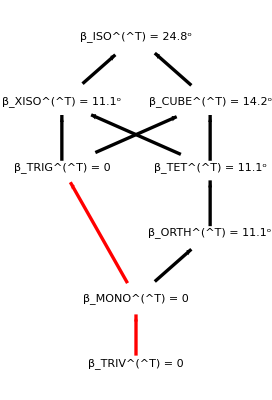

[T] = 1/16(4 (8-√3) | -8 | 3 √2 | -6 √2 | -3 √6 | 0
-8 | 4 (8+√3) | 3 √2 | 6 √2 | -3 √6 | 0
3 √2 | 3 √2 | 76 | -2 √3 | 12 √3 | 4 √3
-6 √2 | 6 √2 | -2 √3 | 24 | 6 | 0
-3 √6 | -3 √6 | 12 √3 | 6 | 52 | 4
0 | 0 | 4 √3 | 0 | 4 | 88)

#### ISO (there is no example in TT21; this is from elastic_mapping_iso.nb)

```mathematica
TT21ISO=({{3, 0, 0, 0, 0, 0}, {0, 3, 0, 0, 0, 0}, {0, 0, 3, 0, 0, 0}, {0, 0, 0, 3, 0, 0}, {0, 0, 0, 0, 3, 0}, {0, 0, 0, 0, 0, 1}});
```

```mathematica
MatrixNote[TT21ISO]="T is TT21ISO"
PrintVoigt[TT21ISO];
MatrixForm[N[TT21ISO]]
```

T is TT21ISO

The [T]_𝔹𝔹 matrix is (3 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 1)

The eigenvalues are: {3,3,3,3,3,1}

The Voigt matrix is (7/3 | -2/3 | -2/3 | 0 | 0 | 0
-2/3 | 7/3 | -2/3 | 0 | 0 | 0
-2/3 | -2/3 | 7/3 | 0 | 0 | 0
0 | 0 | 0 | 3/2 | 0 | 0
0 | 0 | 0 | 0 | 3/2 | 0
0 | 0 | 0 | 0 | 0 | 3/2)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 0   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0, (Angle between T and 𝒯_ISO)

Since β_ISO^(□  T) = 0, then T is assigned symmetry ISO.

Lamé parameters for T are λ = -2/3 and μ = 3/2, Poisson is -2/5

(3. | 0. | 0. | 0. | 0. | 0.
0. | 3. | 0. | 0. | 0. | 0.
0. | 0. | 3. | 0. | 0. | 0.
0. | 0. | 0. | 3. | 0. | 0.
0. | 0. | 0. | 0. | 3. | 0.
0. | 0. | 0. | 0. | 0. | 1.)

#### lattice for TT21ISO:

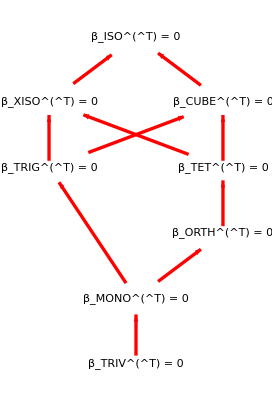

[T] = 1(3 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 1)

#### The “defeat” map of TapeTape2021, Section 15.8. (Using the minimization approach of TapeTape2022, its symmetry is identified as monoclinic.)

```mathematica
denominator=160;
TmatDefeat=1/denominator({{252, -12 √6, -52, 16 √6, -24 √2, 0}, {-12 √6, 180, 12 √6, 6, 2 √3, -32}, {-52, 12 √6, 252, 4 √6, -36 √2, 0}, {16 √6, 6, 4 √6, 211, -23 √3, -48}, {-24 √2, 2 √3, -36 √2, -23 √3, 257, -16 √3}, {0, -32, 0, -48, -16 √3, 288}});
```

```mathematica
MatrixNote[TmatDefeat]="T is Defeat"
PrintVoigt[TmatDefeat];
MatrixForm[N[TmatDefeat]]
```

T is Defeat

The [T]_𝔹𝔹 matrix is (63/40 | -(3 √(3/2))/20 | -13/40 | (√(3/2))/5 | -3/(10 √2) | 0
-(3 √(3/2))/20 | 9/8 | (3 √(3/2))/20 | 3/80 | (√3)/80 | -1/5
-13/40 | (3 √(3/2))/20 | 63/40 | (√(3/2))/20 | -9/(20 √2) | 0
(√(3/2))/5 | 3/80 | (√(3/2))/20 | 211/160 | -(23 √3)/160 | -3/10
-3/(10 √2) | (√3)/80 | -9/(20 √2) | -(23 √3)/160 | 257/160 | -(√3)/10
0 | -1/5 | 0 | -3/10 | -(√3)/10 | 9/5)

The eigenvalues are: {2,2,2,1,1,1}

The Voigt matrix is (1/240 (401+16 √6) | 5/24-1/(5 √6) | 1/240 (-19+16 √6) | -(3 √(3/2))/20 | 1/240 (-3-8 √6) | -(√(3/2))/10
5/24-1/(5 √6) | 1/60 (83-8 √6) | 5/24-1/(5 √6) | (√(3/2))/20 | 1/120 (3-4 √6) | -(√(3/2))/20
1/240 (-19+16 √6) | 5/24-1/(5 √6) | 1/240 (401+16 √6) | (√(3/2))/10 | 1/240 (-3-8 √6) | (3 √(3/2))/20
-(3 √(3/2))/20 | (√(3/2))/20 | (√(3/2))/10 | 63/80 | -(3 √(3/2))/40 | -13/80
1/240 (-3-8 √6) | 1/120 (3-4 √6) | 1/240 (-3-8 √6) | -(3 √(3/2))/40 | 9/16 | (3 √(3/2))/40
-(√(3/2))/10 | -(√(3/2))/20 | (3 √(3/2))/20 | -13/80 | (3 √(3/2))/40 | 63/80)

1-9-2024 12:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = (√(174/5))/5   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.31 = 17.74^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (1.44 | 0. | 0. | 0. | 0. | 0.
0. | 1.44 | 0. | 0. | 0. | 0.
0. | 0. | 1.44 | 0. | 0. | 0.
0. | 0. | 0. | 1.44 | 0. | 0.
0. | 0. | 0. | 0. | 1.44 | 0.
0. | 0. | 0. | 0. | 0. | 1.8)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 3/25 and μ = 18/25, Poisson is 1/14

(1.575 | -0.183712 | -0.325 | 0.244949 | -0.212132 | 0.
-0.183712 | 1.125 | 0.183712 | 0.0375 | 0.0216506 | -0.2
-0.325 | 0.183712 | 1.575 | 0.0612372 | -0.318198 | 0.
0.244949 | 0.0375 | 0.0612372 | 1.31875 | -0.248982 | -0.3
-0.212132 | 0.0216506 | -0.318198 | -0.248982 | 1.60625 | -0.173205
0. | -0.2 | 0. | -0.3 | -0.173205 | 1.8)

```mathematica
cmin=0;cmax=16; dc=2;
contours[TmatDefeat]=Range[cmin,cmax,dc];
MaxForScaling[TmatDefeat]=cmax-dc;
```

```mathematica
tpert[TmatDefeat]=1.89;
```

#### lattice for TmatDefeat:

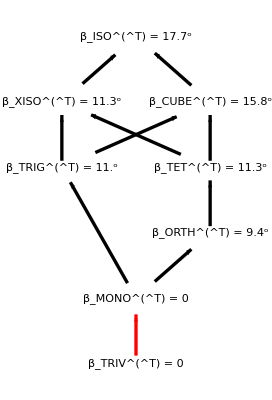

[T] = 1/160(252 | -12 √6 | -52 | 16 √6 | -24 √2 | 0
-12 √6 | 180 | 12 √6 | 6 | 2 √3 | -32
-52 | 12 √6 | 252 | 4 √6 | -36 √2 | 0
16 √6 | 6 | 4 √6 | 211 | -23 √3 | -48
-24 √2 | 2 √3 | -36 √2 | -23 √3 | 257 | -16 √3
0 | -32 | 0 | -48 | -16 √3 | 288)

## List a subset of TRIV maps

#### TRIV maps

```mathematica
TmatallTRIV={TmatBrownAn00,TmatBrownAn25,TmatBrownAn37,TmatBrownAn48,TmatBrownAn60,TmatBrownAn67,TmatBrownAn78,TmatBrownAn96,TmatIgel,TmatMar17,TmatIgel,TmatRussell,TmatLokajicek,TT21TRIV};
```

#### TT24 maps (Mar17 is included in TmatallTRIV)

```mathematica
TmatallTT24={TT24MONOa,TT24MONOb,TT24ORTHa,TT24ORTHb,TT24TETa,TT24TETb};
```

#### display the maps

```mathematica
TmatTable[Tmatall_,numdig_]:=TableForm[Flatten[Table[{{Tlab[Tmat],MatrixShortNote[Tmat],DispMat[Tmat,numdig]},{Spacer[0],Spacer[0],Spacer[1]}},{Tmat,Tmatall}],1]]
```

```mathematica
TmatTable[TmatallTRIV,2]
```

BrownAn00 | An00 | (50.00 | -4.80 | -14.40 | -9.30 | 10.91 | -7.10
-4.80 | 53.80 | 1.20 | -5.50 | -14.49 | -2.12
-14.40 | 1.20 | 67.20 | -5.50 | 6.64 | -13.64
-9.30 | -5.50 | -5.50 | 94.10 | 48.15 | 36.99
10.91 | -14.49 | 6.64 | 48.15 | 149.23 | -18.48
-7.10 | -2.12 | -13.64 | 36.99 | -18.48 | 189.27)
 |  | 
BrownAn25 | An25 | (45.80 | -2.60 | -10.40 | -12.00 | 3.46 | -2.20
-2.60 | 58.00 | 1.60 | -2.50 | -7.22 | 1.06
-10.40 | 1.60 | 70.00 | -5.90 | 8.26 | -14.53
-12.00 | -2.50 | -5.90 | 87.10 | 35.39 | 28.74
3.46 | -7.22 | 8.26 | 35.39 | 133.43 | -8.44
-2.20 | 1.06 | -14.53 | 28.74 | -8.44 | 207.57)
 |  | 
BrownAn37 | An37 | (47.20 | -2.20 | -9.60 | -12.90 | -3.18 | 0.90
-2.20 | 66.20 | 2.80 | -4.90 | -11.37 | 1.55
-9.60 | 2.80 | 71.00 | -6.40 | 7.16 | -13.88
-12.90 | -4.90 | -6.40 | 96.70 | 40.18 | 28.66
-3.18 | -11.37 | 7.16 | 40.18 | 141.70 | -4.67
0.90 | 1.55 | -13.88 | 28.66 | -4.67 | 219.10)
 |  | 
BrownAn48 | An48 | (45.80 | -2.00 | -7.60 | -8.90 | 2.83 | 3.02
-2.00 | 66.00 | 4.20 | -4.90 | -10.68 | 1.80
-7.60 | 4.20 | 71.20 | -9.10 | 0.40 | -13.39
-8.90 | -4.90 | -9.10 | 101.50 | 44.92 | 27.52
2.83 | -10.68 | 0.40 | 44.92 | 144.43 | 1.18
3.02 | 1.80 | -13.39 | 27.52 | 1.18 | 232.87)
 |  | 
BrownAn60 | An60 | (44.40 | 0.40 | 2.80 | -10.50 | 2.48 | 4.00
0.40 | 66.20 | 5.60 | -0.50 | -1.79 | 3.59
2.80 | 5.60 | 73.60 | 0.90 | -9.18 | -11.27
-10.50 | -0.50 | 0.90 | 94.30 | 33.66 | 22.86
2.48 | -1.79 | -9.18 | 33.66 | 133.57 | 2.07
4.00 | 3.59 | -11.27 | 22.86 | 2.07 | 231.03)
 |  | 
BrownAn67 | An67 | (48.00 | 1.40 | 0.60 | -8.30 | 6.87 | 7.51
1.40 | 71.00 | 6.40 | 0.80 | 0.58 | 6.21
0.60 | 6.40 | 74.60 | 7.20 | -7.16 | -10.86
-8.30 | 0.80 | 7.20 | 102.50 | 35.39 | 19.80
6.87 | 0.58 | -7.16 | 35.39 | 147.10 | 5.16
7.51 | 6.21 | -10.86 | 19.80 | 5.16 | 236.10)
 |  | 
BrownAn78 | An78 | (46.60 | 1.60 | 1.80 | -6.90 | 4.45 | 10.45
1.60 | 65.60 | 9.00 | 2.20 | 3.00 | 8.41
1.80 | 9.00 | 70.00 | -6.90 | 1.91 | -17.15
-6.90 | 2.20 | -6.90 | 99.40 | 34.18 | 19.43
4.45 | 3.00 | 1.91 | 34.18 | 129.20 | 5.09
10.45 | 8.41 | -17.15 | 19.43 | 5.09 | 247.10)
 |  | 
BrownAn96 | An96 | (49.20 | 6.00 | -4.40 | -2.00 | 2.19 | 19.27
6.00 | 73.20 | 10.40 | -1.60 | 4.39 | 7.43
-4.40 | 10.40 | 72.00 | 3.60 | -12.24 | -13.39
-2.00 | -1.60 | 3.60 | 102.20 | 33.14 | 18.21
2.19 | 4.39 | -12.24 | 33.14 | 127.87 | 10.70
19.27 | 7.43 | -13.39 | 18.21 | 10.70 | 266.23)
 |  | 
Igel | Igel | (10.00 | 0.70 | 1.05 | 5.20 | -3.93 | -3.10
0.70 | 8.00 | -2.00 | -0.20 | -0.46 | 0.33
1.05 | -2.00 | 6.00 | -0.45 | -0.19 | 0.32
5.20 | -0.20 | -0.45 | 5.50 | 0 | -1.22
-3.93 | -0.46 | -0.19 | 0 | 5.50 | 2.12
-3.10 | 0.33 | 0.32 | -1.22 | 2.12 | 13.00)
 |  | 
Mar17 | Mar17 | (206.20 | -67.40 | 17.10 | -15.90 | 166.60 | -19.50
-67.40 | 352.90 | 32.20 | 3.30 | 61.60 | -41.60
17.10 | 32.20 | 343.80 | 0.40 | 73.60 | -4.20
-15.90 | 3.30 | 0.40 | 270.00 | 88.80 | 13.30
166.60 | 61.60 | 73.60 | 88.80 | 287.10 | 30.70
-19.50 | -41.60 | -4.20 | 13.30 | 30.70 | 74.00)
 |  | 
Igel | Igel | (10.00 | 0.70 | 1.05 | 5.20 | -3.93 | -3.10
0.70 | 8.00 | -2.00 | -0.20 | -0.46 | 0.33
1.05 | -2.00 | 6.00 | -0.45 | -0.19 | 0.32
5.20 | -0.20 | -0.45 | 5.50 | 0 | -1.22
-3.93 | -0.46 | -0.19 | 0 | 5.50 | 2.12
-3.10 | 0.33 | 0.32 | -1.22 | 2.12 | 13.00)
 |  | 
Russell | Russ | (132.35 | 0.09 | 0 | 0 | 0 | 0
0.09 | 149.24 | 0 | 0 | 0 | 0
0 | 0 | 143.93 | 0.58 | 0.11 | 0.17
0 | 0 | 0.58 | 151.12 | -10.09 | -15.90
0 | 0 | 0.11 | -10.09 | 143.72 | 6.75
0 | 0 | 0.17 | -15.90 | 6.75 | 450.32)
 |  | 
Lokajicek | Loka | (33.60 | -0.40 | -0.40 | -0.10 | -0.17 | 0.24
-0.40 | 33.60 | 0.20 | 0.50 | 1.10 | -2.86
-0.40 | 0.20 | 33.60 | -0.10 | -0.98 | -4.33
-0.10 | 0.50 | -0.10 | 32.65 | 0.72 | 1.63
-0.17 | 1.10 | -0.98 | 0.72 | 34.42 | -1.04
0.24 | -2.86 | -4.33 | 1.63 | -1.04 | 83.33)
 |  | 
TT21TRIV | TRIV | (1 | 0 | 0 | -2/5 | 0 | 0
0 | 6/5 | 0 | 0 | -2/5 | 0
0 | 0 | 1 | 0 | 0 | 0
-2/5 | 0 | 0 | 1 | 0 | 0
0 | -2/5 | 0 | 0 | 6/5 | 0
0 | 0 | 0 | 0 | 0 | 6/5)
 |  |

```mathematica
TmatTable[TmatallTT24,0]
```

TT24MONOa | MONOa | (1 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 3 | 2 | 1 | 0
0 | 0 | 2 | 4 | 0 | 0
0 | 0 | 1 | 0 | 5 | 0
0 | 0 | 0 | 0 | 0 | 6)
 |  | 
TT24MONOb | MONOb | (28 | -2 | 0 | 0 | 0 | 0
-2 | 61 | 0 | 0 | 0 | 0
0 | 0 | 71 | -4 | 6 | 8
0 | 0 | -4 | 68 | 10 | 0
0 | 0 | 6 | 10 | 62 | -3
0 | 0 | 8 | 0 | -3 | 59)
 |  | 
TT24ORTHa | ORTHa | (86 | 0 | 0 | 0 | 0 | 0
0 | 51 | 0 | 0 | 0 | 0
0 | 0 | 32 | 0 | 0 | 0
0 | 0 | 0 | 46 | -20 | 13
0 | 0 | 0 | -20 | 45 | -2
0 | 0 | 0 | 13 | -2 | 87)
 |  | 
TT24ORTHb | ORTHb | (1 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 5 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)
 |  | 
TT24TETa | TETa | (60 | 0 | 0 | 0 | 0 | 0
0 | 60 | 0 | 0 | 0 | 0
0 | 0 | 15 | 0 | 0 | 0
0 | 0 | 0 | 71 | 0 | 0
0 | 0 | 0 | 0 | 58 | 6
0 | 0 | 0 | 0 | 6 | 15)
 |  | 
TT24TETb | TETb | (2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 1)
 |  |

```mathematica
Tblank=({{□, □, □, □, □, □}, {□, □, □, □, □, □}, {□, □, □, □, □, □}, {□, □, □, □, □, □}, {□, □, □, □, □, □}, {□, □, □, □, □, □}});
```